## functions

```mathematica
Off[InterpolatingFunction::dmval];
Off[InterpolatingFunction::dval];
Off[InterpolatingFunction::dmwarn];
Off[InterpolatingFunction::dzero];
```

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinuteString[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
MinuteOfDayToHourAndMinuteList[minuteOfDay_]:={IntegerPart[minuteOfDay/60],FractionalPart[minuteOfDay/60]60}
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
DateExtend[dateObject_,hour_,minute_]:=DateObject[Flatten[{DateList[dateObject][[1;;3]],{hour,minute}}]]
```

```mathematica
(*Function to normalize DateObjects to the same granularity*)
NormalizeDate[date_]:=DateObject[DateList[date][[1;;3]]]

(*Function to find the index of the first element not less than a given date*)
FindFirstIndexNotLessThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<normDate,low=mid+1,high=mid];];
low]

(*Function to find the index of the first element greater than a given date*)
FindFirstIndexGreaterThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<=normDate,low=mid+1,high=mid];];
low]

(*Define the function to select elements by date range*)
SelectElementsByDateRange[list_,startDate_,endDate_]:=Module[{startIndex,endIndex,normStartDate,normEndDate},(*Normalize dates*)normStartDate=NormalizeDate[startDate];
normEndDate=NormalizeDate[endDate];
(*Find the starting and ending indices*)startIndex=FindFirstIndexNotLessThan[list,normStartDate];
endIndex=FindFirstIndexGreaterThan[list,normEndDate];
(*Return the sublist within the range*)list[[startIndex;;endIndex-1]]]
```

```mathematica
MapFunctionToGranularity[function_,data_List,granularity_String]:=Module[
{extractedComponents,groupedData,mappedData},
(*Extract the relevant component (e.g.,month) from each DateObject and pair with value*)extractedComponents=({DateValue[#[[1]],granularity],#[[2]]}&/@data);
(*Group data by the extracted component and calculate the mean for each group*)
groupedData=GroupBy[extractedComponents,First->Last];
(*Replace each group key with an average value*)
mappedData=function/@groupedData;
SortBy[Transpose[{Keys[mappedData],Values[mappedData]}],First]
]
```

```mathematica
dayNameToDayOfWeek={"Mon"->1,"Tue"->2,"Wed"->3,"Thu"->4,"Fri"->5,"Sat"->6,"Sun"->7};
```

```mathematica
RemoveOutliers[list_,sd_]:=Module[{mean,stdDev,lowerBound,upperBound},mean=Mean[list];
stdDev=StandardDeviation[list];
lowerBound=mean-sd stdDev;
upperBound=mean+sd stdDev;
Select[list,lowerBound<=#<=upperBound&]]
```

## misc

## heatmeter read-in

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinute[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
path=formattedDataRoot;
fileName="heat_stock_net.csv";
lastLoadDay=Module[
{dirs,sortedDirs,foundFile},
(*Get list of directories*)
dirs=FileNames["*",path];
(*Sort directories in decreasing order*)
sortedDirs=Sort[dirs,DateObject[#1]>DateObject[#2]&];
(*Search for the file*)
foundFile=SelectFirst[sortedDirs,FileExistsQ[FileNameJoin[{#,fileName}]]&];
StringSplit[foundFile,"\\"][[-1]]
];
loadDayStamps=Map[StringRiffle[Map[ToStringWithDateCorrection,#[[1;;3]]],"-"]&,DateRange[{2024,2,1},DateObject[lastLoadDay]]];
heatStockDataOriginal=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
heatStockDataNet=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
badDays=Flatten[Intersection[Flatten[Position[heatStockDataOriginal,$Failed]],Flatten[Position[heatStockDataNet,$Failed]]]];
goodDays=Complement[Range[Length[loadDayStamps]],badDays];
Manipulate[
Module[
{dayN,timeStamps},
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=Map[
HourAndMinuteToMinuteOfDay[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
];
Grid[{
{"day","original","net","diff"},
{
loadDayStamps[[dayN]],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={}&&Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]]-heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"]
},
Table[ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Nothing]
},
Joined->True,PlotRange->All,Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.25]}&,Range[0,24 60, 120]],Automatic},ImageSize->250,PlotLabel->"cycle "<>ToString[cycle],Prolog->{If[showCaptures,{Pink,Thin,Map[Line[{{#,0},{#,10000}}]&,timeStamps]}]}
],{cycle,1,4}]
}]
],
{showCaptures,{False,True}},
{{day,loadDayStamps[[goodDays]][[-1]]},loadDayStamps[[goodDays]]}
]
```

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

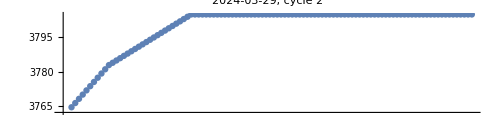
-Graphics-
1500 | 1510 | 1520 | 1530 | 1540 | 1550 | 1600 | 1610 | 1620 | 1630 | 1640 | 1650 | 1700 | 1710 | 1720 | 1730 | 1740 | 1750 | 1800 | 1810 | 1820 | 1830 | 1840 | 1850 | 1900 | 1910 | 1920 | 1930 | 1940 | 1950 | 2000 | 2010 | 2020 | 2030 | 2040 | 2050 | 2100 | 2110 | 2120 | 2130 | 2140 | 2150 | 2200 | 2210 | 2220 | 2230 | 2240 | 2250 | 2300 | 2310 | 2320 | 2330 | 2340 | 2350
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
cycle=2;timeSpan={15,24}100;
day=loadDayStamps[[goodDays]][[-1]];
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=DeleteDuplicates[Map[
ToExpression[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
]];
cycleImagesForTimeSpan=Map[
Import[rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"<>ToStringWithDateCorrection[#,4]<>"_"<>ToString[cycle]<>".png"]
&,Select[timeStamps,Between[#,timeSpan]&]];
{
ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing]
},
Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.5]}&,Range[0,24 60, 10]],Automatic},ImageSize->500,AspectRatio->0.25,PlotLabel->day<>", cycle "<>ToString[cycle]
],
{Select[timeStamps,Between[#,timeSpan]&],cycleImagesForTimeSpan}//Grid
}//Column
```

```mathematica
heatFlowDataOriginal=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow.csv"]&,
loadDayStamps];
```

```mathematica
heatFlowDataNet=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow_net.csv"]&,
loadDayStamps];
```

```mathematica
Table[
Table[
ListPlot[
{
Transpose[Transpose[heatFlowDataOriginal[[day]]][[{1,1+cycle}]]],
Transpose[Transpose[heatFlowDataNet[[day]]][[{1,1+cycle}]]]
},
Joined->True,PlotRange->All
]
,{cycle,1,4}]
,{day,goodDays}]//Grid
```

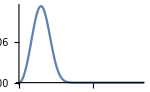
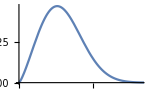
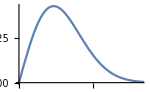
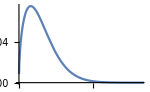

```mathematica
weibullParameters={
{3,10.3,0.001},
{2.3,20,0.001},
{2,20,0.001},
{1.5,10,0.001}
};
Table[Plot[
PDF[WeibullDistribution[weibullParameters[[cycle]][[1]],weibullParameters[[cycle]][[2]],weibullParameters[[cycle]][[3]]],power],{power,0,100},PlotRange->{{0,50},All},ImageSize->150
],{cycle,1,4}]//Row
```

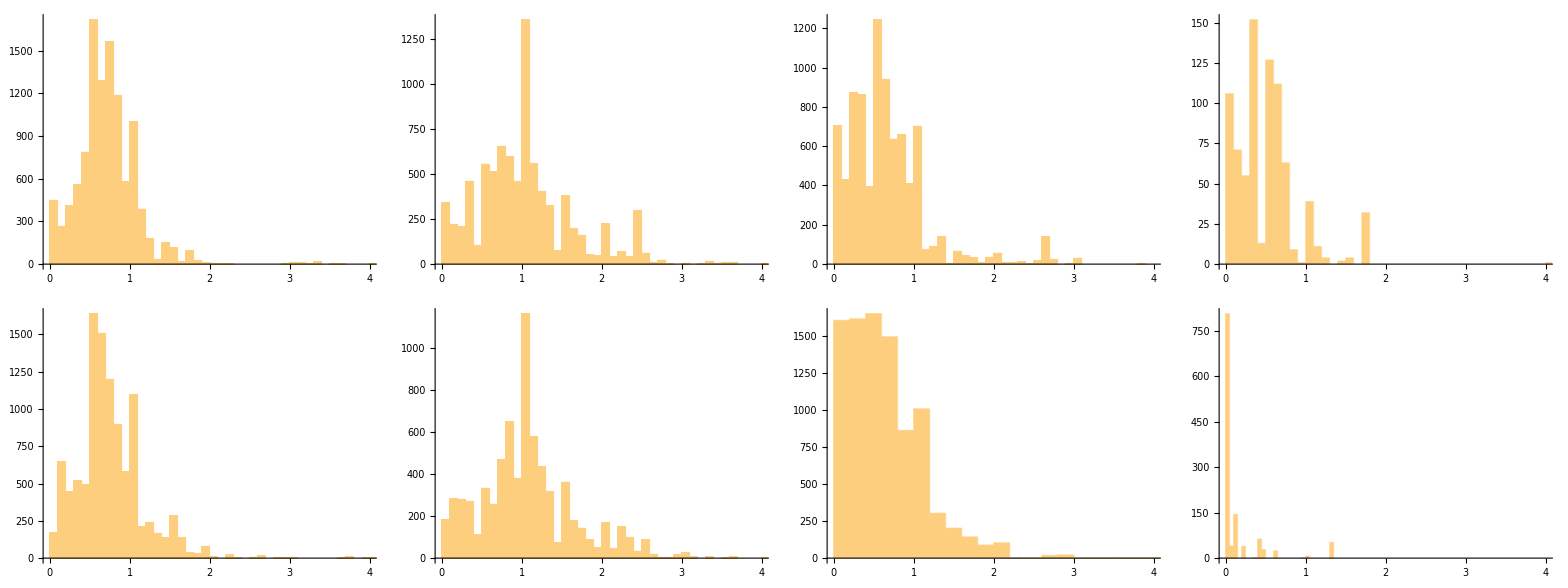

```mathematica
{
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataOriginal[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}],
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataNet[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}]
}//Grid
```

## adatok

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
seasonDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

## hő

```mathematica
heatDataDays=Map[DateObject,DateRange[{2023,11,22},{2024,3,29}]];
```

```mathematica
heatStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatDataDays]]];
```

```mathematica
heatStockDated=Map[Flatten[#,1]&,Transpose[Table[
Module[
{dayDateList},
dayDateList=DateList[heatDataDays[[dayN]]];
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatStockLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],heatStockLine[[2;;5]]}]
,{heatStockLine,heatStockPre[[dayN]]}]]
]
,{dayN,1,Length[heatDataDays]}]]];
(*1-es kör átfordulás: jan 20-21*)
(*2-es kör átfordulás: feb 4-5*)
```

```mathematica
cycle=2;
Map[
SortBy[heatStock[[cycle]][[#[[1]];;#[[1]]+1]],First]&,
Map[Position[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#][[1]]&,Select[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#<-10&]]
]
```

{{{Thu 14 Dec 2023 23:55:00GMT+2,4247},{Fri 15 Dec 2023 00:00:00GMT+2,4228.81}},{{Sun 4 Feb 2024 23:55:00GMT+2,9937},{Mon 5 Feb 2024 00:00:00GMT+2,125.}}}

```mathematica
heatStockDated[[1]]=Map[
If[
DateObject[{2024,1,20,23,59}]<#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[1]]];
```

```mathematica
heatStockDated[[2]]=Quiet[Map[
If[
DateObject[{2024,2,4,23,59}]<=#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[2]]]];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDated.mx",heatStock];
```

```mathematica
heatStockSeason=Table[
Transpose[{
Transpose[heatStockDated[[cycle]]][[1]],
Transpose[heatStockDated[[cycle]]][[2]]-heatStockDated[[cycle]][[1]][[2]]
}],{cycle,1,4}];
```

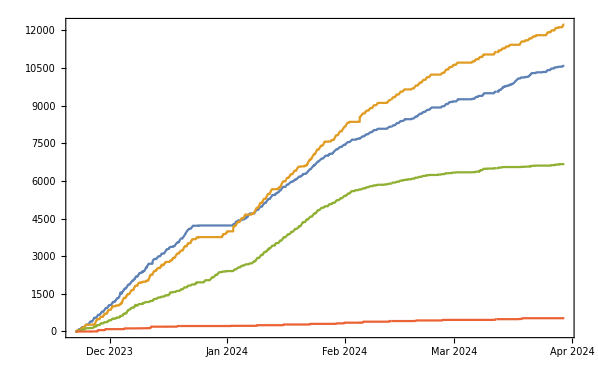

```mathematica
DateListPlot[heatStockSeason]
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockSeason.mx",heatStockSeason];
```

```mathematica
heatStockSeason=Import[NotebookDirectory[]<>"\\heatStockSeason.mx"];
```

```mathematica
heatStockDaily=Table[Table[
Module[
{dailyCumulative},
dailyCumulative=SelectElementsByDateRange[heatStockSeason[[cycle]],DateExtend[day,0,0],DateExtend[day,23,59]];
If[
dailyCumulative!={},
Transpose[{
Transpose[dailyCumulative][[1]],
Transpose[dailyCumulative][[2]]-dailyCumulative[[1]][[2]]
}],
None]
]
,{day,seasonDays}],{cycle,1,4}];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDaily.mx",heatStockDaily];
```

```mathematica
heatStockDaily=Import[NotebookDirectory[]<>"\\heatStockDaily.mx"];
```

## gáz

```mathematica
gasDataDays=Map[DateObject,Join[
DateRange[{2023,11,23},{2023,12,6}],
DateRange[{2023,12,15},{2024,5,16}]
]];
```

```mathematica
gasStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\gas_stock.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,gasDataDays]]];
```

```mathematica
gasStockDaily=Table[
If[
MemberQ[gasDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[gasDataDays,day][[1]][[1]];
dayDateList=DateList[gasDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[gasStockLine[[1]]];
Transpose[{DateObject[dayDateList],gasStockLine[[2]]}]
,{gasStockLine,gasStockPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\gasStockDaily.mx",gasStockDaily];
```

```mathematica
gasStockDaily=Import[NotebookDirectory[]<>"\\gasStockDaily.mx"];
```

## szobák hőmérséklete

```mathematica
roomTempDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
roomTempsPre=Table[Quiet[
Map[
Import[formattedDataRoot<>"\\"<>#<>"\\room_"<>ToString[room]<>"_temps.csv"]
&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,roomTempDataDays]]
],{room,1,10}];
```

```mathematica
roomTempsDaily=Table[Table[
If[
MemberQ[roomTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[roomTempDataDays,day][[1]][[1]];
dayDateList=DateList[roomTempDataDays[[dayN]]];
If[
Dimensions[roomTempsPre[[room]][[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[roomTempLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],roomTempLine[[2;;5]]}]
,{roomTempLine,roomTempsPre[[room]][[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}],{room,1,10}];
```

```mathematica
Export[NotebookDirectory[]<>"\\roomTempsDaily.mx",roomTempsDaily];
```

```mathematica
roomTempsDaily=Import[NotebookDirectory[]<>"\\roomTempsDaily.mx"];
```

```mathematica
setTempLowForAtLeastOneRoomDaily=Transpose[
{roomTempDataDays,
Quiet[Map[
Min[#]<0&,
Transpose[Table[
Table[
Min[Select[Transpose[roomTemp[[1]]][[2]]-Transpose[roomTemp[[2]]][[2]],NumberQ]]
,{roomTemp,roomTempsDaily[[room]]}]
,{room,1,10}]]
]]
}];
```

## fűtési állapot

```mathematica
heatingStateDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
heatingStatePre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heating_state.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatingStateDataDays]]];
```

```mathematica
heatingStateDaily=Table[
If[
MemberQ[heatingStateDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[heatingStateDataDays,day][[1]][[1]];
dayDateList=DateList[heatingStateDataDays[[dayN]]];
If[
Dimensions[heatingStatePre[[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatingStateLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],5],heatingStateLine[[2;;6]]}]
,{heatingStateLine,heatingStatePre[[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}];
```

```mathematica
Position[heatingStateDaily,None]
```

{{56},{57},{96},{97},{110},{111},{119},{120},{138},{145},{146},{152},{153},{154},{157},{158},{159},{160},{161},{162},{163},{167},{168},{173},{174},{175},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192}}

```mathematica
heatingStateNoDataDays=heatingStateDataDays[[Flatten[Position[heatingStatePre,$Failed]]]];
```

```mathematica
noHeatingDays=Transpose[Select[setTempLowForAtLeastOneRoomDaily,#[[2]]==False&]][[1]];
```

```mathematica
Table[
Module[
{dayDateList,minutes,blankDayData,dayPosition},
dayDateList=DateList[day];
minutes=Map[
DateObject[Join [dayDateList[[1;;3]],MinuteOfDayToHourAndMinuteList[#]]]&
,Transpose[heatingStatePre[[1]]][[1]]];
blankDayData=ConstantArray[
Transpose[
{
minutes,
ConstantArray[0,288]
}
],5];
dayPosition=Position[seasonDays,day][[1]][[1]];
heatingStateDaily[[dayPosition]]=blankDayData;
]
,{day,Intersection[heatingStateNoDataDays,noHeatingDays]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Position[heatingStateDaily,None]
```

{{95},{96},{109},{110},{153},{162},{166},{167},{172},{174}}

```mathematica
Export[NotebookDirectory[]<>"\\heatingStateDaily.mx",heatingStateDaily];
```

```mathematica
heatingStateDaily=Import[NotebookDirectory[]<>"\\heatingStateDaily.mx"];
```

## egyéb

### külső hőmérséklet

```mathematica
externalTempDataDays=Complement[Map[DateObject,DateRange[{2023,11,22},{2024,5,16}]]];
```

```mathematica
externalTempPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\external_temp.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,externalTempDataDays]]];
```

```mathematica
externalTempDaily=Table[
If[
MemberQ[externalTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[externalTempDataDays,day][[1]][[1]];
dayDateList=DateList[externalTempDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[externalTempLine[[1]]];
Transpose[{DateObject[dayDateList],externalTempLine[[2]]}]
,{externalTempLine,externalTempPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\externalTempDaily.mx",externalTempDaily];
```

```mathematica
externalTempDaily=Import[NotebookDirectory[]<>"\\externalTempDaily.mx"];
```

### környezeti változók

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
gasPricePerCubicMeter=700;
```

```mathematica
airSpecificMass=1.2;(*kg/m3*)
```

```mathematica
airSpecificHeatCapacity=1012;(*J/kg/K*)
```

```mathematica
roomNames={"ovi","PK","SZGK","Gólyairoda","Mérce","vendégtér","kisterem","trafóház","Oktopusz","Lahmacun","Kazán közös terek","műhely"};
```

```mathematica
roomsWithTempData={1,2,3,4,5,6,7,9,10};
```

```mathematica
roomToCycle={1,1,2,2,2,3,3,4,1,2};
roomsByCycle=Table[Flatten[Position[roomToCycle,cycle]],{cycle,1,4}];
```

```mathematica
roomAreas={53,26,29,26.5,72,100,60.25,240,66,24,50,26.5} ;
```

```mathematica
roomExternalWallLength={9.8,4.8,5.4,6,10.2,15.4,10.2,25,12.5,5.2,None,2.5} ;
```

```mathematica
roomHeight=3.2;
```

```mathematica
radiatorHeight=0.6;
roomRadiatorLength={4 140,280,300,180,540+150,6 120,4 120,0,2 140,100}/100;
```

## elemzés

## jegyzetek

úgy érdemes tekinteni, mint egy cél felé hajtott rendszert

kontrollváltozók:
	- fő kontrollváltozók: fogyasztott gáz és kiküldött hő
		> korrellált kontrollváltozók: fűtési állapot
	- nem irányított kontrollváltozó: kinti hőmérséklet, besugárzás
függő változók: szobák hőmérséklete

hibajel: beállított hőmérséklet - aktuális hőmérséklet

fő kérdések:
- milyen költséggel milyen mértékben lehet csökkenteni a hibát?
- hogy teljesít a rendszer, lehet-e jellemezni valahogy?
- külső körülmények hogyan befolyásolják?
- van-e olyan szcenárió, amivel jelentősen jobban teljesítene?
- lehet-e jellemezni a szobákat?
- hogyan viszonyul a tavalyi adatokhoz?

- pontosítani a szobák hőtechnikai jellemzőit (homennyisegbol becsülni? figyelembe venni aktuális hőmérsékletet hokapacitashoz? fűtővíz hőmérséklete?)
- karakterizalni, h milyen költsége van  egy szoba felfutesenek adott külső hőmérséklet mellett 
- jellemezni a szitut költség - komfort síkon, akár szezonon belül is
- modellezni, hogy szabályozás vagy beavatkozás mennyit tol a síkon milyen irányba

## gázból hő

### nem fűtésre elmenő gáz becslése

```mathematica
gasFlowAndHeatingStateDaily=Select[Quiet[Table[
Module[
{gasDataPosition,heatingStateDataPosition},
gasDataPosition=Position[gasDataDays,day];
heatingStateDataPosition=Position[heatingStateDataDays,day];
If[
Dimensions[gasStockDaily[[gasDataPosition[[1]][[1]]]]]!={},
Transpose[Join[
{
Drop[Transpose[gasStockDaily[[gasDataPosition[[1]][[1]]]]][[1]],1],
Differences[Transpose[gasStockDaily[[gasDataPosition[[1]][[1]]]]][[2]]]
},
Map[
Drop[Transpose[#][[2]],1]
&,heatingStateDaily[[heatingStateDataPosition[[1]][[1]]]]]
]],
None
]
],{day,seasonDays}]],Length[Dimensions[#]]>1&];
```

```mathematica
gasConsumptionByHeatingState=Table[
Transpose[Transpose[Select[
Flatten[gasFlowAndHeatingStateDaily,1],
#[[3]]==heatingState&
]][[{1,2}]]],{heatingState,0,1}];
```

```mathematica
nonHeatingProportionOfGasConsumption=Mean[Transpose[gasConsumptionByHeatingState[[1]]][[2]]]/Total[Mean[Transpose[gasConsumptionByHeatingState[[1]]][[2]]]+Mean[Transpose[gasConsumptionByHeatingState[[2]]][[2]]]];
```

```mathematica
nonHeatingProportionOfGasConsumption=0.3707982073738875;
heatingProportionOfGasConsumption=1-nonHeatingProportionOfGasConsumption;
```

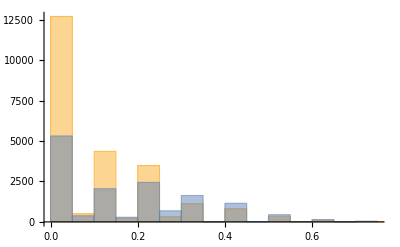

```mathematica
Histogram[
{
Transpose[gasConsumptionByHeatingState[[1]]][[2]],
Transpose[gasConsumptionByHeatingState[[2]]][[2]]
}]
```

```mathematica
typicalDailyGasConsumptionByMonthByHeatingState=Table[Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
Select[
gasConsumptionByHeatingState[[heating]],
DateValue[#[[1]],"Month"]==month&
],"Hour"]]]
,{heating,1,2}],{month,{11,12,1,2,3,4}}];
```

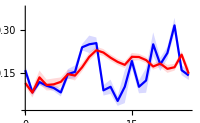
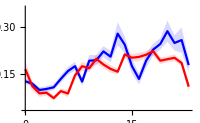
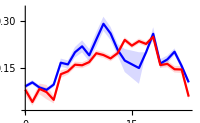
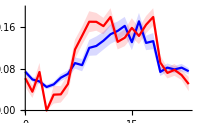
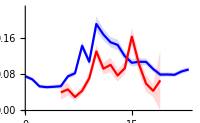
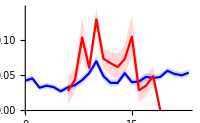

```mathematica
Table[
ErrorListPlot[
typicalDailyGasConsumptionByMonthByHeatingState[[month]],
{Blue,Red},
{ImageSize->200,PlotLegends->{"nincs fűtés","van fűtés"}},
{True,True,False}
],{month,1,6}]
```

```mathematica
typicalDailyGasConsumptionByHeatingState=Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
gasConsumptionByHeatingState[[heating]],"Hour"]]]
,{heating,1,2}];
```

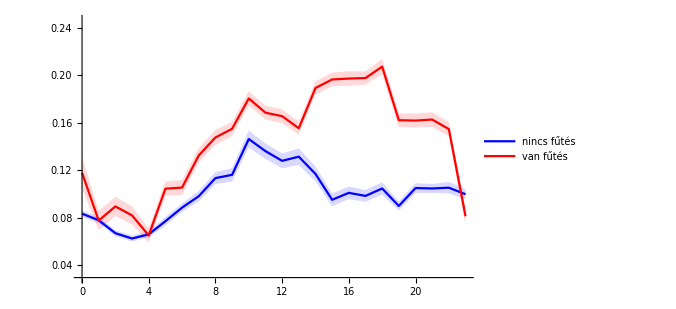

```mathematica
ErrorListPlot[
typicalDailyGasConsumptionByHeatingState,
{Blue,Red},
{ImageSize->500,PlotLegends->{"nincs fűtés","van fűtés"}},
{True,True,False}
]
```

```mathematica
typicalWeeklyGasConsumptionByHeatingState=Table[
Transpose[
Map[
{#[[1]],#[[2]],#[[3]]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,gasConsumptionByHeatingState[[heating]],"DayName"]/.{Monday->1,Tuesday->2,Wednesday->3,Thursday->4,Friday->5,Saturday->6,Sunday->7}]
,First]
]
]
,{heating,1,2}];
```

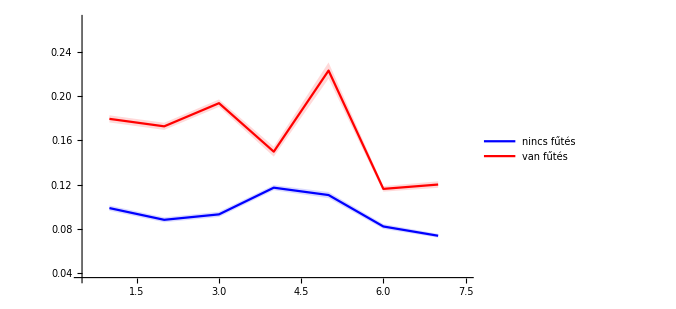

```mathematica
ErrorListPlot[
typicalWeeklyGasConsumptionByHeatingState,
{Blue,Red},
{ImageSize->500,PlotLegends->{"nincs fűtés","van fűtés"}},
{True,True,False}
]
```

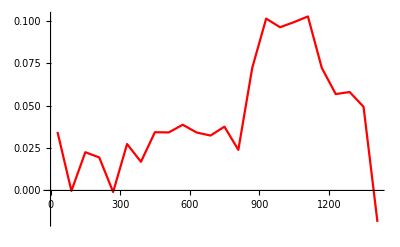

```mathematica
ListPlot[Transpose[{
typicalDailyGasConsumptionByHeatingState[[1]][[1]]60+30,
typicalDailyGasConsumptionByHeatingState[[2]][[2]]-typicalDailyGasConsumptionByHeatingState[[1]][[2]]
}],Joined->True,PlotStyle->Red]
```

```mathematica
NonHeatingGasConsumption[minute_]:=Quiet[Interpolation[
Transpose[{
typicalDailyGasConsumptionByHeatingState[[1]][[1]]60+30,
typicalDailyGasConsumptionByHeatingState[[1]][[2]]
}],InterpolationOrder->0
][minute]]
```

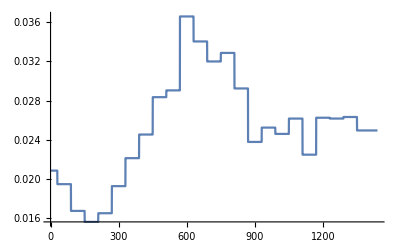

```mathematica
Plot[
NonHeatingGasConsumption[minute]/4,{minute,0,24 60}
]
```

```mathematica
Total[Table[
NonHeatingGasConsumption[minute],
{minute,0,60 24-5,5}]]/4
```

7.25604

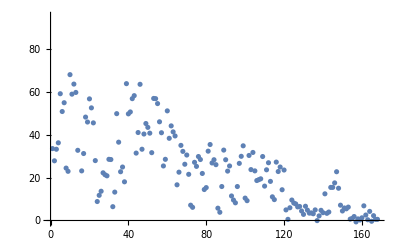

```mathematica
ListPlot[
Map[
Transpose[#][[2]][[-1]]-Total[Table[
NonHeatingGasConsumption[minute]/4,
{minute,0,60 24-5,5}]]
&,DeleteCases[gasStockDaily,None]]
]
```

```mathematica
totalGasTotalHeatDaily=Table[
{
day[[1]][[-1]][[2]] energyContentInGasPerCubicMeter,
Total[Table[day[[2]][[cycle]][[-1]][[2]],{cycle,1,4}]]
}
,{day,gasAndHeatStockDaily}];
```

```mathematica
Fit[totalGasTotalHeatDaily,{1,x},x]
```

0.193335+0.601838 x

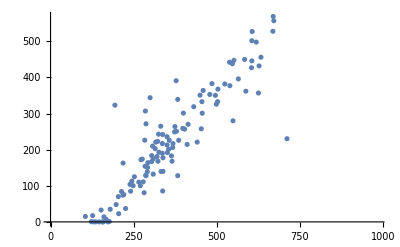

```mathematica
ListPlot[totalGasTotalHeatDaily]
```

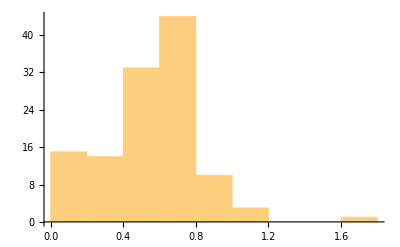

```mathematica
Histogram[Map[#[[2]]/#[[1]]&,totalGasTotalHeatDaily]]
```

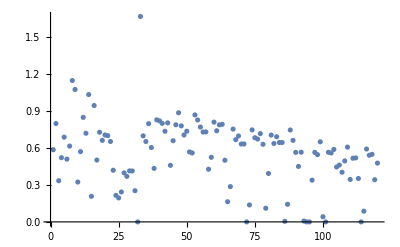

```mathematica
ListPlot[Map[#[[2]]/#[[1]]&,totalGasTotalHeatDaily]]
```

### kazánok hatékonyságának becslése

```mathematica
gasStockAndHeatStockDaily=Quiet[Table[
If[
Dimensions[gasStockDaily[[dayN[[1]][[1]]]]]!={}&&Dimensions[heatStockDaily[[1]][[dayN[[1]][[1]]]]]!={},
{
gasStockDaily[[dayN[[1]][[1]]]],
Table[heatStockDaily[[cycle]][[dayN[[1]][[1]]]],{cycle,1,4}]
},
None
],{dayN,1,Length[seasonDays]}]];
```

```mathematica
heatingProportionOfGasConsumption
```

0.629202

```mathematica
boilerEfficiencyHourlyByDay=Quiet[ Select[Table[
Transpose[{
Map[DateObject[Join[DateList[Transpose[dayData[[1]]][[1]][[1]]][[1;;3]],{#,30,0}]]&,Range[0,23]],
Transpose[MapFunctionToGranularity[Total,Transpose[{Drop[Transpose[dayData[[1]]][[1]],1],Total[Table[Differences[Transpose[dayData[[2]][[cycle]]][[2]]],{cycle,1,4}]]}],"Hour"]][[2]]/(0.75 Transpose[MapFunctionToGranularity[Total,Transpose[{Drop[Transpose[dayData[[1]]][[1]],1],Differences[Transpose[dayData[[1]]][[2]]]}],"Hour"]][[2]] energyContentInGasPerCubicMeter)
}],{dayData,DeleteCases[gasStockAndHeatStockDaily,None]}],NumberQ[Total[Transpose[#][[2]]]]&]];
```

```mathematica
meanBoilerEfficiencyByDay=Table[
Select[Transpose[dayData][[2]],NumberQ[#]&&0<#&]//If[#!={},{NormalizeDate[dayData[[1]][[1]]],Mean[#]},Nothing]&
,{dayData,boilerEfficiencyHourlyByDay}];
```

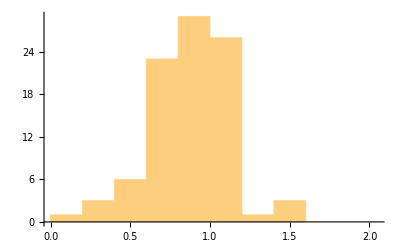

```mathematica
Histogram[Transpose[meanBoilerEfficiencyByDay][[2]]]
```

```mathematica
boilerEfficiencyEstimate=Mean[Transpose[meanBoilerEfficiencyByDay][[2]]];
boilerEfficiencyEstimate=0.9835433845947968;
```

Part::partw: Part 2 of Transpose[meanBoilerEfficiencyByDay] does not exist.

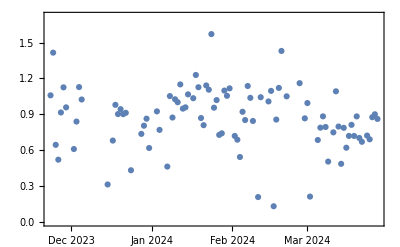

```mathematica
DateListPlot[meanBoilerEfficiencyByDay,Joined->False]
```

## szobák hődinamikája

```mathematica
HeatingCurve[externalTemp_,maxTemp_,minTemp_]:=Module[{supplyTemp},(*Define the relationship between external temperature and supply water temperature*)supplyTemp=If[externalTemp<=-10,maxTemp,If[externalTemp>=25,minTemp,maxTemp-(maxTemp-minTemp)/(25+10)(externalTemp+10)]];
supplyTemp]
```

### hőkarakterisztikák becslése

#### burkolófelületek hőkonduktivitása (W/K)

```mathematica
calculationSpan=30;
spanError=0.1;
minTempDiffAcrossWall=3;
roomEnvelopeThermalResistanceEstimations=Table[
Module[
{roomHeatCapacity,calculationData,timeVector,TimeNearestFunction,PositionFinder},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
calculationData=Select[Flatten[DeleteCases[Table[If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[
{
dayN 24 60+Range[5,24 60,5],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Transpose[externalTempDaily[[dayN]]][[2]]
}
],
None
],{dayN,1,Length[seasonDays]}],None],1],NumberQ[Total[#]]&];
timeVector=Transpose[calculationData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,periodData,Δt,ΔT,externalTempAverage,roomTempAverage,periodDerivedParameters,Tdiff},
pos2=PositionFinder[calculationData[[pos1]][[1]]+calculationSpan];
periodData=calculationData[[pos1;;pos2]];
Δt=(periodData[[-1]][[1]]-periodData[[1]][[1]]);
periodDerivedParameters={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Total[Transpose[periodData][[2]]]==0,(*2 no heating during period*)
Min[Differences[Transpose[periodData][[3]]]]<0,(*3 monotonous cooling during period*)
Mean[Transpose[periodData][[3]]],(*4 avg room temp*)
Mean[Transpose[periodData][[4]]],(*5 avg external temp*)
Quiet[(periodData[[-1]][[3]]-periodData[[1]][[3]])/(60Δt)](*6 ΔT / Δt*)
};
Tdiff=periodDerivedParameters[[4]]-periodDerivedParameters[[5]];
If[
periodDerivedParameters[[1]]&&
periodDerivedParameters[[2]]&&
periodDerivedParameters[[3]]&&
minTempDiffAcrossWall<=Tdiff&&
periodDerivedParameters[[6]]<0&&
roomHeatCapacity periodDerivedParameters[[6]]!=0,
Tdiff/Abs[(roomHeatCapacity periodDerivedParameters[[6]])],(*R_total calculation*)
Nothing
]
],{pos1,1,Length[calculationData]}]
]
,{room,1,10}];
```

```mathematica
Export[NotebookDirectory[]<>"roomEnvelopeThermalResistanceEstimations.mx",roomEnvelopeThermalResistanceEstimations]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\roomEnvelopeThermalResistanceEstimations.mx

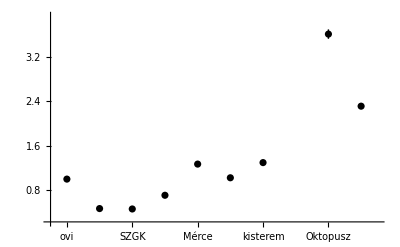

```mathematica
ErrorListPlot[
{
Transpose[Map[Flatten,Transpose[{Range[10],Map[GetMeanAndSEM[1/#]&,roomEnvelopeThermalResistanceEstimations]}][[roomsWithTempData]]]]
},
{Black},
{Ticks->{Transpose[{Range[10],Map[Rotate[#,Pi/2]&,roomNames[[1;;10]]]}],Automatic}},
{False,False,True}
]
```

```mathematica
roomEnvelopeThermalConductivities=Map[Mean[1/#]&,roomEnvelopeThermalResistanceEstimations];(*K/W*)
```

```mathematica
roomEnvelopeThermalConductivities={0.9982577999173019,0.46863221112434744,0.4613273636460981,0.7076400111322203,1.2682439879749117,1.0221875156356737,1.2950835880618299,None,3.605230507310251,2.309339847023162};
```

#### radiátorok konvektív hőátadási tényezője (W/m^2 K)

```mathematica
calculationSpan=10;
spanError=0.1;
roomRadiatorConvectiveHeatTransferCoefficientEstimations=Table[
Module[
{roomHeatCapacity,roomEnvelopeThermalConductivity,roomRadiatorArea,calculationData,timeVector,TimeNearestFunction,PositionFinder},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomEnvelopeThermalConductivity=roomEnvelopeThermalConductivities[[room]];
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
calculationData=Select[Flatten[DeleteCases[Table[If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[
{
dayN 24 60+Range[5,24 60,5],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Transpose[externalTempDaily[[dayN]]][[2]],
Map[HeatingCurve[#,64,45]&,Transpose[externalTempDaily[[dayN]]][[2]]]
}
],
None
],{dayN,1,Length[seasonDays]}],None],1],NumberQ[Total[#]]&];
timeVector=Transpose[calculationData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,periodData,Δt,ΔT,externalTempAverage,roomTempAverage,periodDerivedParameters,TdiffExt,TdiffHeater,Qroom,Qheater,Qwall},
pos2=PositionFinder[calculationData[[pos1]][[1]]+calculationSpan];
periodData=calculationData[[pos1;;pos2]];
Δt=(periodData[[-1]][[1]]-periodData[[1]][[1]]);
periodDerivedParameters={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Mean[Transpose[periodData][[2]]]==1,(*2 constant heating during period*)
Min[Differences[Transpose[periodData][[3]]]]>0,(*3 monotonous warming during period*)
Mean[Transpose[periodData][[3]]],(*4 avg room temp*)
Mean[Transpose[periodData][[4]]],(*5 avg external temp*)
Mean[Transpose[periodData][[5]]],(*6 avg heater temp*)
Quiet[(periodData[[-1]][[3]]-periodData[[1]][[3]])/(60Δt)](*7 ΔT / Δt*)
};
TdiffExt=periodDerivedParameters[[4]]-periodDerivedParameters[[5]];
TdiffHeater=periodDerivedParameters[[6]]-periodDerivedParameters[[4]];
Qwall=TdiffExt roomEnvelopeThermalConductivity;
Qroom=roomHeatCapacity periodDerivedParameters[[7]];
Qheater=Qroom+Qwall;
If[
periodDerivedParameters[[1]]&&
periodDerivedParameters[[2]]&&
periodDerivedParameters[[3]]&&
periodDerivedParameters[[7]]>0&&
roomHeatCapacity periodDerivedParameters[[7]]!=0,
Qheater/(roomRadiatorArea TdiffHeater),(*h calculation*)
Nothing
]
]
,{pos1,1,Length[calculationData]}]
]
,{room,1,10}];
```

```mathematica
Map[Length,roomRadiatorConvectiveHeatTransferCoefficientEstimations]
```

{4718,2069,5014,4095,5871,2603,6043,0,275,228}

```mathematica
Export[NotebookDirectory[]<>"roomRadiatorConvectiveHeatTransferCoefficientEstimations.mx",roomRadiatorConvectiveHeatTransferCoefficientEstimations]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\roomRadiatorConvectiveHeatTransferCoefficientEstimations.mx

```mathematica
roomRadiatorConvectiveHeatTransferCoefficients={0.15250229638926738,0.168703360142732,0.16873584837102043,0.4008207756252688,0.15917869450450967,0.1431452552523042,0.2362745543903207,None,0.5166470326430609,3.1308364744008643};
```

```mathematica
roomRadiatorThermalConductivities={1.0248154317358766,0.5668432900795795,0.6074490541356735,0.8657728753505807,1.31799959049734,1.2367750053799085,1.360941433288247,0.,1.7359340296806842,3.757003769281037};
```

#### értelmezés

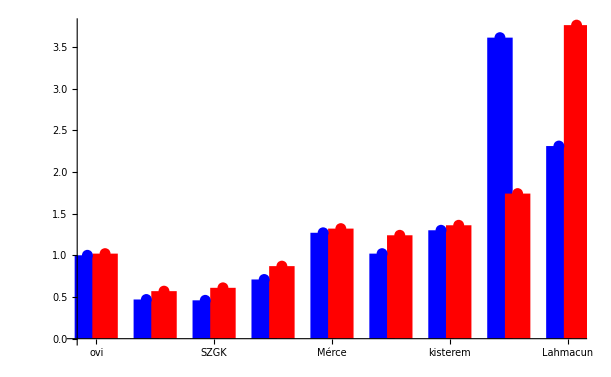

```mathematica
ListPlot[
{
Transpose[{
Range[9]-0.15,
Round[roomEnvelopeThermalConductivities,0.01][[roomsWithTempData]]
}],
Transpose[{
Range[9]+0.15,
Round[(2roomRadiatorLength radiatorHeight)roomRadiatorConvectiveHeatTransferCoefficients,0.01][[roomsWithTempData]]
}]
},
PlotRange->All,PlotStyle->{Blue,Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

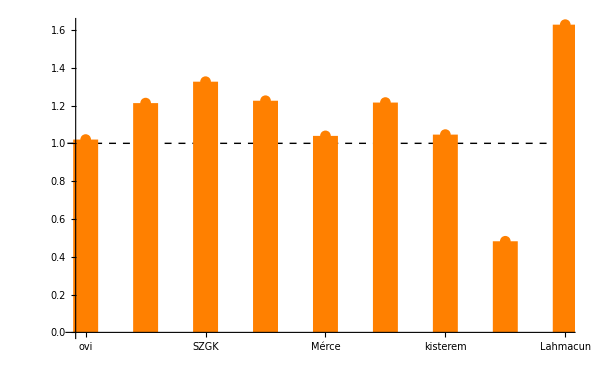

```mathematica
ListPlot[
Round[(2roomRadiatorLength radiatorHeight)roomRadiatorConvectiveHeatTransferCoefficients,0.01][[roomsWithTempData]]/Round[roomEnvelopeThermalConductivities,0.01][[roomsWithTempData]],
PlotRange->All,PlotStyle->{Orange},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},
Prolog->{Dashed,Line[{{0,1},{10,1}}]}
]
```

### hőfelvételi arányok szobánként

```mathematica
fullHeatDynamics=Quiet[
Table[
Table[
Table[
Module[
{dayN,roomEnvelopeThermalConductivity,roomRadiatorThermalConductivity,roomTemp,externalTemp,heaterTemp,tempDiffExt,tempDiffHeater,roomExternalWallArea,heatLoss,roomRadiatorArea,heatGain},
dayN=Position[seasonDays,day][[1]][[1]];
roomEnvelopeThermalConductivity=roomEnvelopeThermalConductivities[[room]];
roomRadiatorThermalConductivity=roomRadiatorThermalConductivities[[room]];
roomTemp=Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
heaterTemp=Map[HeatingCurve[#,65,45]&,Transpose[externalTempDaily[[dayN]]][[2]]];
tempDiffExt=roomTemp-externalTemp;
tempDiffHeater=heaterTemp-roomTemp;
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
heatLoss= tempDiffExt roomEnvelopeThermalConductivity;
heatGain=tempDiffHeater roomRadiatorThermalConductivity Transpose[heatingStateDaily[[dayN]][[1+cycle]]][[2]];
Transpose[{
Transpose[externalTempDaily[[dayN]]][[1]],
Transpose[heatingStateDaily[[dayN]][[1+cycle]]][[2]],
100Differences[Transpose[heatStockDaily[[cycle]][[dayN]]][[2]]]//Flatten[{#[[1]],#[[1;;-1]]}]&,
heatGain,
heatLoss,
externalTemp,
roomTemp
}]
]
,{day,Drop[heatDataDays,1]}]
,{room,Flatten[Position[roomToCycle,cycle]]}]
,{cycle,1,3}]
];
```

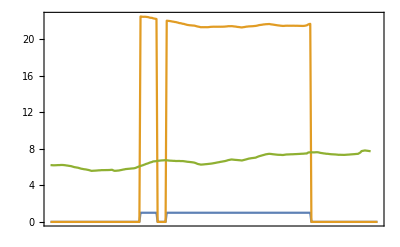

```mathematica
DateListPlot[
{
Transpose[Transpose[Quiet[fullHeatDynamics[[2]][[1]][[30]]]][[{1,2}]]],
Transpose[Transpose[Quiet[fullHeatDynamics[[2]][[1]][[30]]]][[{1,4}]]],
Transpose[Transpose[Quiet[fullHeatDynamics[[2]][[1]][[30]]]][[{1,5}]]]
}
]
```

```mathematica
heatingPeriodHeatDynamics=Table[
roomsOnCycle=Flatten[Position[roomToCycle,cycle]];
Select[
Module[
{dataForSeasonByRoom,heatingStateSwitch,heatingPeriods},
dataForSeasonByRoom=Table[Quiet[Select[Flatten[fullHeatDynamics[[cycle]][[roomOnCycleN]],1],ListQ]],{roomOnCycleN,1,Length[roomsOnCycle]}];
heatingStateSwitch=Differences[Transpose[dataForSeasonByRoom[[1]]][[2]]];
heatingPeriods=Transpose[{
Map[First,Position[heatingStateSwitch,1]],
Map[First,Position[heatingStateSwitch,-1]]
}];
Table[
{
Total[Transpose[dataForSeasonByRoom[[1]][[heatingPeriod[[1]]+1;;Min[heatingPeriod[[2]]+5,Length[dataForSeasonByRoom[[1]]]]]]][[3]]],
Table[
Module[
{heatingPeriodDataForRoom},
heatingPeriodDataForRoom=dataForSeasonByRoom[[roomOnCycleN]][[heatingPeriod[[1]]+1;;Min[heatingPeriod[[2]]+5,Length[dataForSeasonByRoom[[1]]]]]];
If[
Max[Differences[Map[UnixTime,Transpose[heatingPeriodDataForRoom][[1]]]]]<30 60,
Table[Total[Transpose[heatingPeriodDataForRoom][[heatGainOrLoss]]],{heatGainOrLoss,4,5}],
{None,None}
]
],{roomOnCycleN,1,Length[roomsOnCycle]}]
}
,{heatingPeriod,heatingPeriods[[1;;{229,191,208}[[cycle]]]]}]
],ListQ]
,{cycle,1,3}];
```

```mathematica
heatSumsForHeatingPeriods=Quiet[Table[Select[Map[
{
#[[1]],
Total[Transpose[#[[2]]][[1]]],
Total[Transpose[#[[2]]][[2]]]
}
&,heatingPeriodHeatDynamics[[cycle]]
],ListQ],{cycle,1,3}]];
```

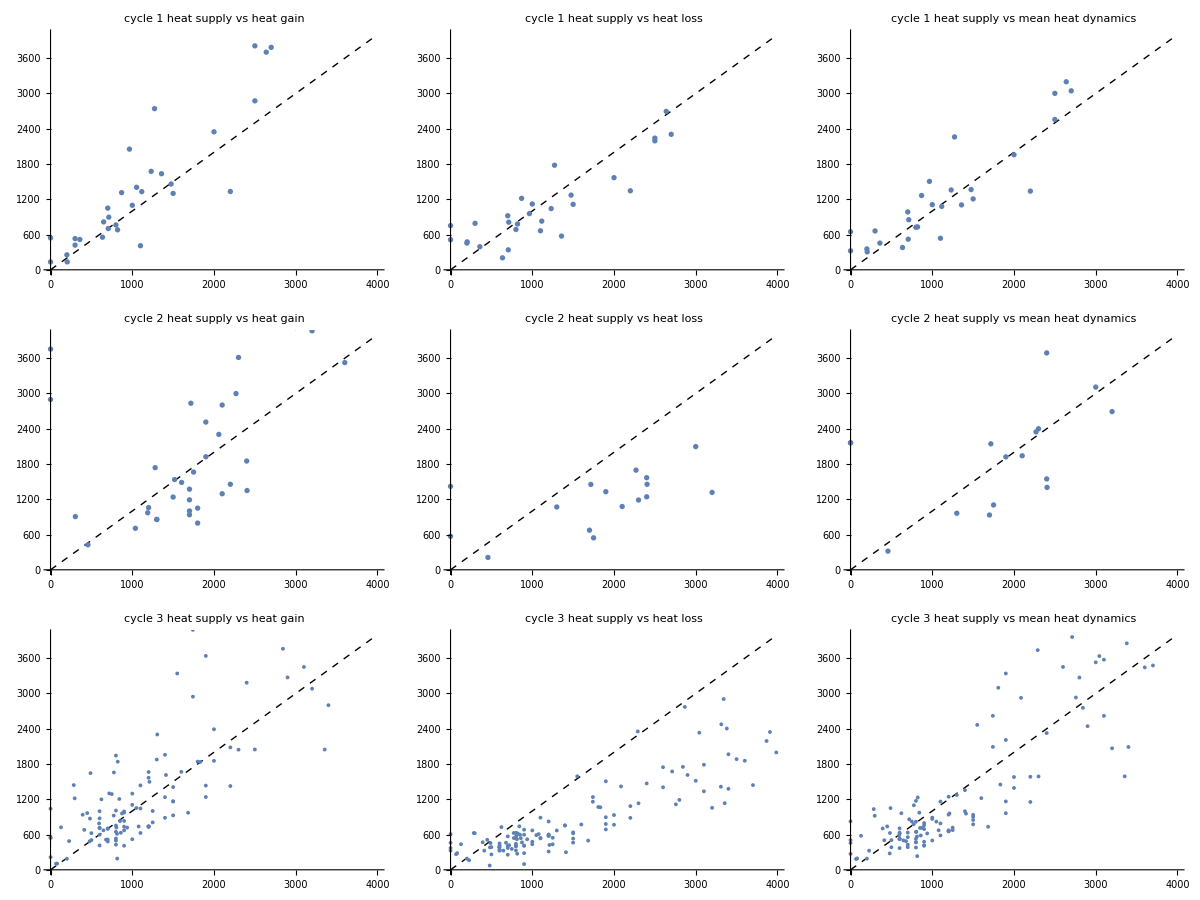

```mathematica
Table[
Join[
Table[
ListPlot[
Quiet[Transpose[Transpose[Select[heatSumsForHeatingPeriods[[cycle]],NumberQ[#[[1]]+#[[heatGainOrLoss]]]&]][[{1,1+heatGainOrLoss}]]]],
ImageSize->300,AspectRatio->1,PlotRange->{{0,4000},{0,4000}},PlotLabel->"cycle "<>ToString[cycle]<>"\nheat supply vs heat "<>{"gain","loss"}[[heatGainOrLoss]],Prolog->{Black,Dashed,Thin,Line[{{0,0},{4000,4000}}]}
]
,{heatGainOrLoss,1,2}],
{
ListPlot[
Transpose[{
Quiet[Transpose[Transpose[Select[heatSumsForHeatingPeriods[[cycle]],NumberQ[#[[1]]+#[[1]]]&]][[1]]]],
Mean[Transpose[Quiet[Transpose[Transpose[Select[heatSumsForHeatingPeriods[[cycle]],NumberQ[#[[1]]+#[[1]]]&]][[{2,3}]]]]]]
}],AspectRatio->1,PlotRange->{{0,4000},{0,4000}},ImageSize->300,Prolog->{Black,Dashed,Thin,Line[{{0,0},{4000,4000}}]},PlotLabel->"cycle "<>ToString[cycle]<>"\nheat supply vs mean heat dynamics"
]
}]
,{cycle,1,3}]//Grid
```

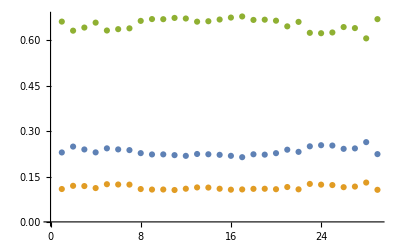
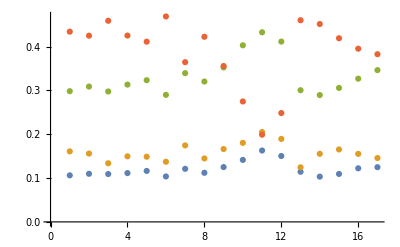
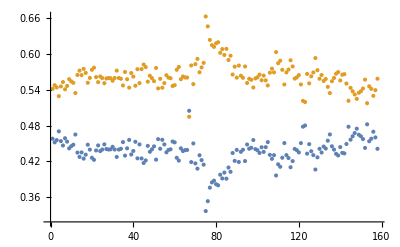

```mathematica
Table[
ListPlot[Transpose[Map[
Transpose[#[[2]]][[heatGainOrLoss]]/Total[Transpose[#[[2]]][[heatGainOrLoss]]]
&,Select[heatingPeriodHeatDynamics[[cycle]],NumberQ[Total[Flatten[#]]]&]
]]],{cycle,1,3}]
```

```mathematica
Map[roomNames[[#]]&,Flatten[Position[roomToCycle,2]]]
```

{SZGK,Gólyairoda,Mérce,Lahmacun}

```mathematica
roomHeatTakeupRatios=Transpose[SortBy[Flatten[Table[
Transpose[{
Flatten[Position[roomToCycle,cycle]],
Mean[
Map[
Transpose[#[[2]]][[heatGainOrLoss]]/Total[Transpose[#[[2]]][[heatGainOrLoss]]]
&,Select[heatingPeriodHeatDynamics[[cycle]],NumberQ[Total[Flatten[#]]]&]
]
]
}],{cycle,1,3}],1],First]][[2]]
```

```mathematica
roomHeatTakeupRatios={0.2328033518572063,0.11396170489798108,0.12027985600187004,0.15847673896227935,0.3330466013238296,0.43663959569809724,0.5633604043019025,None,0.6532349432448127,0.388196803712021};
```

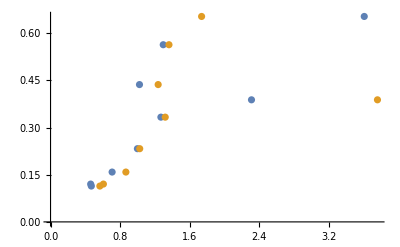

```mathematica
ListPlot[
{
Transpose[{
roomEnvelopeThermalConductivities[[roomsWithTempData]],roomHeatTakeupRatios[[roomsWithTempData]]
}],
Transpose[{
roomRadiatorThermalConductivities[[roomsWithTempData]],roomHeatTakeupRatios[[roomsWithTempData]]
}]
}
]
```

## szezon teljesítménye

### szobák fogyasztása

```mathematica
roomHeatTakeupDaily=Table[
If[
MemberQ[roomsWithTempData,room],
Table[
If[
Dimensions[heatStockDaily[[1]][[dayN]]]!={},
Transpose[{
Transpose[heatStockDaily[[roomToCycle[[room]]]][[dayN]]][[1]],
Differences[Transpose[heatStockDaily[[roomToCycle[[room]]]][[dayN]]][[2]]]roomHeatTakeupRatios[[room]]//Flatten[{#[[1]],#[[1;;-1]]}]&
}],
None
]
,{dayN,1,Length[seasonDays]}],
None]
,{room,1,10}];
```

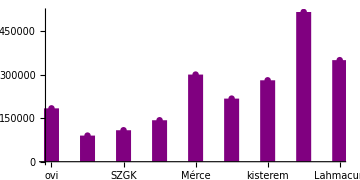

```mathematica
ListPlot[
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}],
PlotRange->All,PlotStyle->{Purple},Filling->Axis,FillingStyle->{Thickness[0.03]},AspectRatio->0.5,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

```mathematica
roomCoolingVsPriceFit=Fit[
Transpose[{
Round[roomEnvelopeThermalConductivities,0.01][[roomsWithTempData]],
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}]/1000
}],
{1,Log[x]},
x
];
```

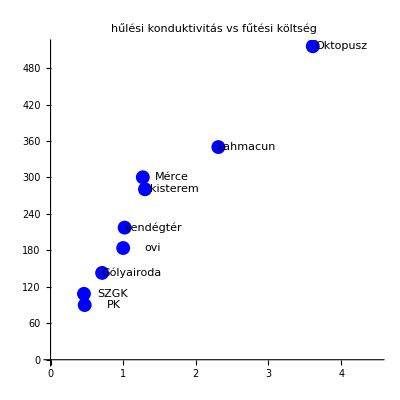

```mathematica
plotData=Transpose[{
Round[roomEnvelopeThermalConductivities,0.01][[roomsWithTempData]],
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}]/1000,
roomNames[[roomsWithTempData]]
}];
ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->"hűlési konduktivitás vs fűtési költség",PlotStyle->{PointSize->0.025,Blue},AspectRatio->1,PlotRange->{{0,4.5},All},
Joined->False,
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{0.4,0}]
}&,plotData]
]
```

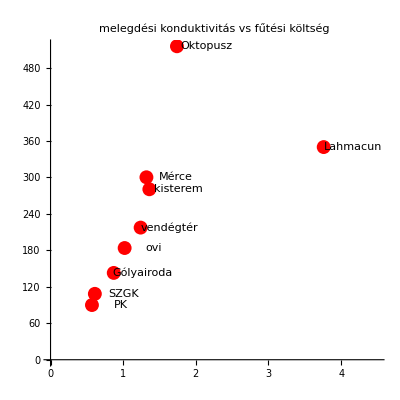

```mathematica
plotData=Transpose[{
Round[roomRadiatorThermalConductivities,0.01][[roomsWithTempData]],
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}]/1000,
roomNames[[roomsWithTempData]]
}];
ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->"melegdési konduktivitás vs fűtési költség",PlotStyle->{PointSize->0.025,Red},AspectRatio->1,PlotRange->{{0,4.5},All},Joined->False,
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{0.4,0}]
}&,plotData]
]
```

### szobák céltartása

```mathematica
roomSetTempDiffDaily=Quiet[Table[
If[
MemberQ[roomsWithTempData,room],Table[
If[
Dimensions[roomsWithTempData[[room]][[dayN]]]!={},
Select[
Transpose[
{
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[1]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]]
}
],NumberQ[#[[2]]]&],
None
]
,{dayN,1,Length[seasonDays]}],
None]
,{room,1,10}]];
```

### költség vs komfort

```mathematica
roomHeatVsTempDiffDaily=Table[
If[
MemberQ[roomsWithTempData,room],
Select[
Quiet[Transpose[{
Map[
If[
 Dimensions[#]!={},
{
NormalizeDate[Transpose[#][[1]][[1]]],
gasPricePerCubicMeter Total[Transpose[#][[2]]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)
},
None
]&,
roomHeatTakeupDaily[[room]]],
Map[
If[
Dimensions[#]!={}&&#!={},
{
NormalizeDate[Transpose[#][[1]][[1]]],
Mean[Select[Transpose[Transpose[#][[{2,3}]]],#[[2]]==1&]][[1]]
},
None
]&,
roomSetTempDiffDaily[[room]]]
}]],
Dimensions[#[[1]]]!={}&&Dimensions[#[[2]]]!={}&
],
None
],{room,1,10}];
```

```mathematica
extTBinWidth=3;
roomPerformanceExternalTempBins=Table[
If[
MemberQ[roomsWithTempData,room],
Module[
{roomPerformaceCharacteristics,externalTempRange,binnedData},
roomPerformaceCharacteristics=Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]],
#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&];
externalTempRange=MinMax[Transpose[roomPerformaceCharacteristics][[3]]];
binnedData=Select[Quiet[Table[
{
extT+extTBinWidth,
Transpose[Transpose[Select[roomPerformaceCharacteristics,Between[#[[1]],{extT,extT+extTBinWidth}]&]][[{2,3}]]]
}
,{extT,Floor[externalTempRange[[1]],1],Ceiling[externalTempRange[[2]],1],extTBinWidth}]],NumberQ[Total[Flatten[#]]]&]
],
None
],{room,1,10}];
```

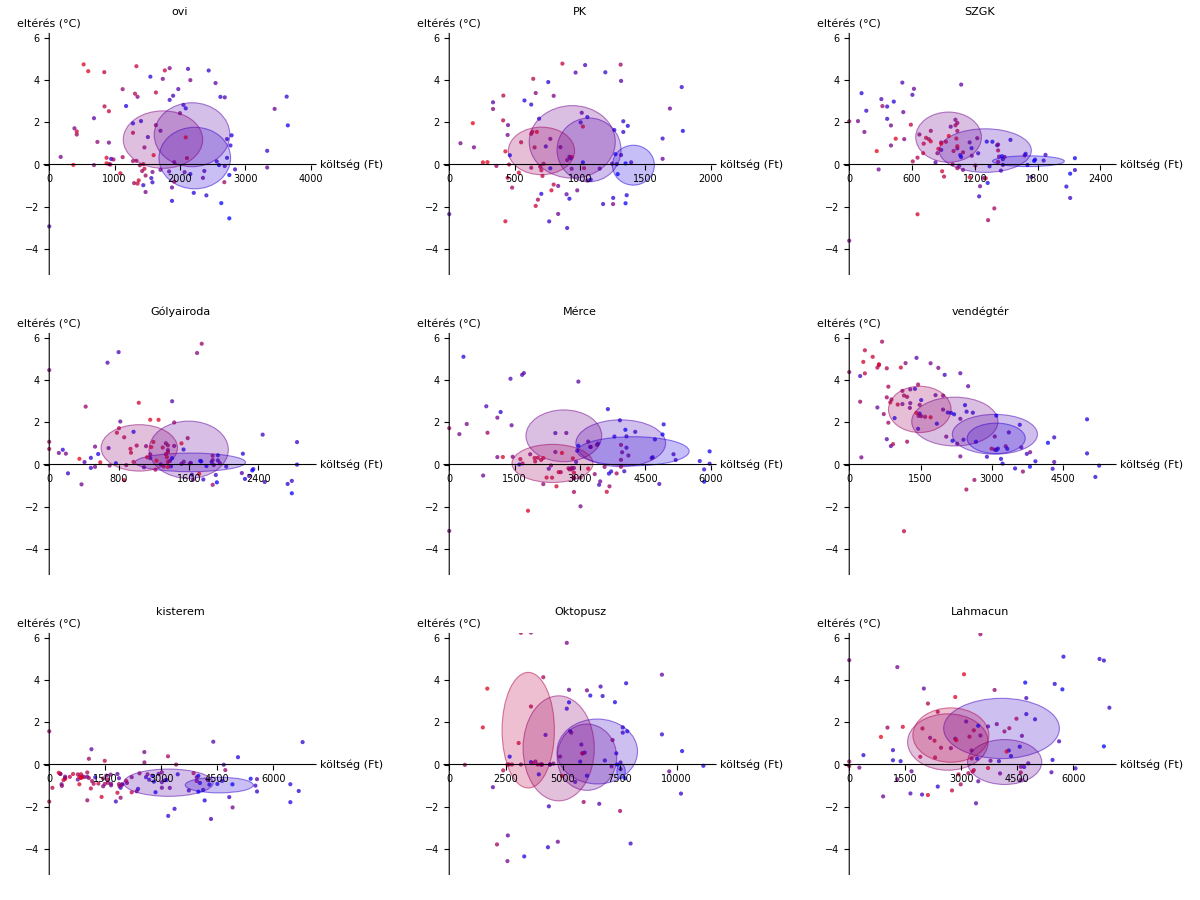

```mathematica
Quiet[Table[
ListPlot[
{},
PlotLabel->roomNames[[room]],
AxesLabel->{Rotate["költség (Ft)",Pi/2],"eltérés (°C)"},
ImageSize->350,
PlotRange->{
{0,
Ceiling[Max[
Map[
#[[1]][[2]]&,
roomHeatVsTempDiffDaily[[room]]]
],500]
},
{-5,6}
},AspectRatio->1,
Prolog->{
Table[
{
RGBColor[
(binData[[1]]+3)/(21-3),
0,
1-(binData[[1]]+3)/(21-3),
0.25
],
EdgeForm[
{
Thick,Dashed,
RGBColor[
(binData[[1]]+3)/(21-3),
0,
1-(binData[[1]]+3)/(21-3),
0.5
]
}
],
Ellipsoid[
GetMeanAndSD[binData[[2]]][[1]],
GetMeanAndSD[binData[[2]]][[2]]0.75
]
},{binData,roomPerformanceExternalTempBins[[room]]}
],
Map[
{
RGBColor[
(#[[1]]+3)/(21-3),
0,
1-(#[[1]]+3)/(21-3),
0.75
],
PointSize->0.0125,
Point[#[[{2,3}]]]
}&,
Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]],
#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&]
]
}
],{room,roomsWithTempData}]]//ArrayReshape[#,{3,3}]&//Grid
```

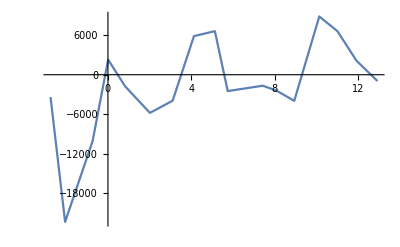
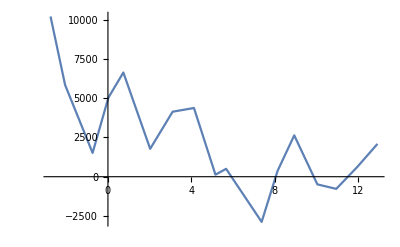
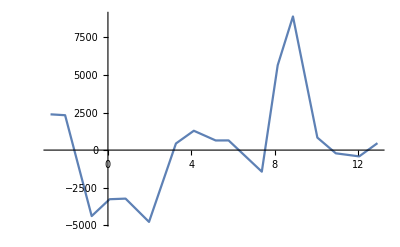
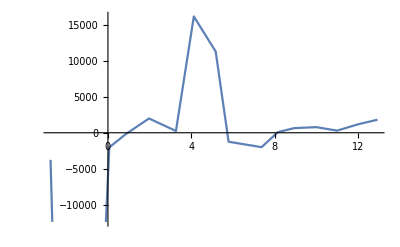
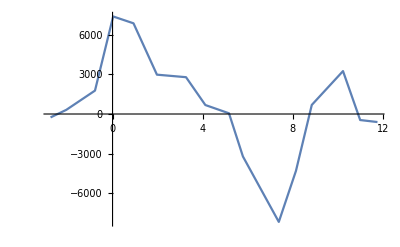
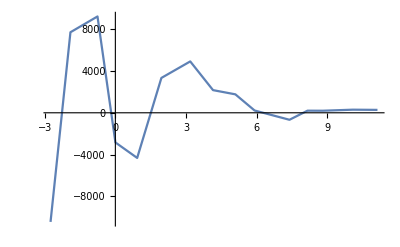
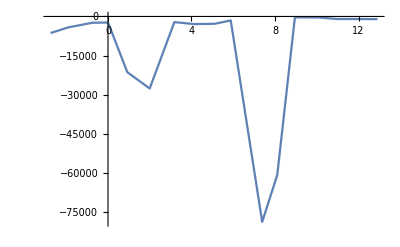
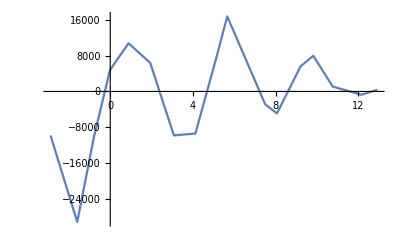

```mathematica
binWidth=2;
binStep=1;
Table[
ListPlot[
Module[
{dataToBin,binRange},
dataToBin=Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]]/#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&];
binRange=MinMax[Transpose[dataToBin][[1]]];
Table[
Mean[Select[dataToBin,Between[#[[1]],{bin-binWidth/2,bin+binWidth/2}]&]]
,{bin,binRange[[1]],binRange[[2]],binStep}]
],Joined->True
],{room,roomsWithTempData}]
```

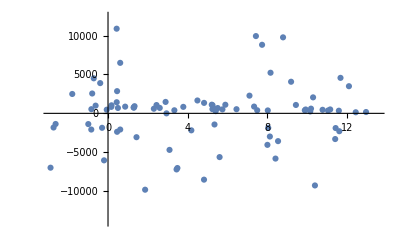
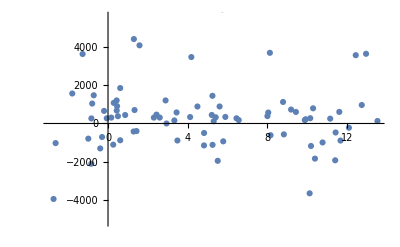
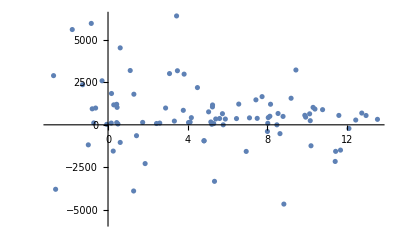
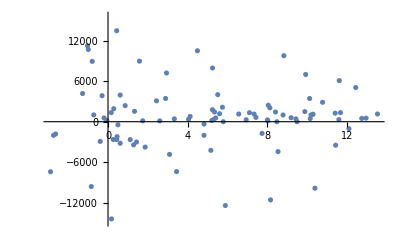
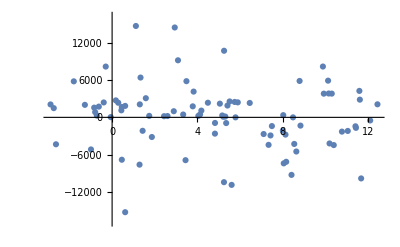
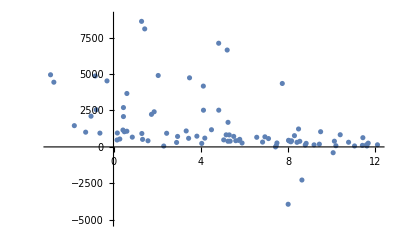
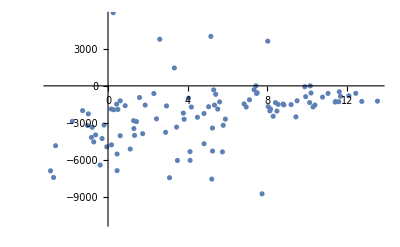
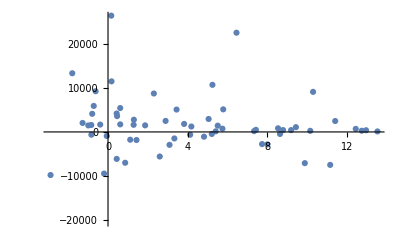

```mathematica
Table[
ListPlot[
Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]]/#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&]
],{room,roomsWithTempData}]
```

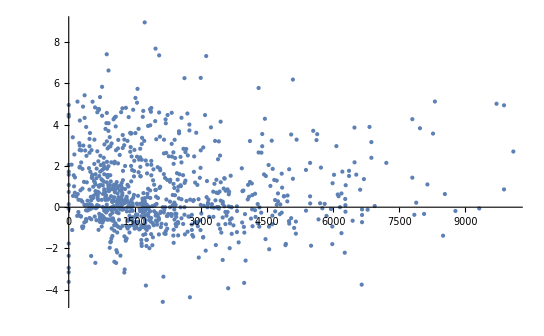

```mathematica
ListPlot[
Flatten[Table[
Select[Map[
{
#[[1]][[2]],
Quiet[#[[2]][[2]]]
}
&,roomHeatVsTempDiffDaily[[room]]],NumberQ[Total[#]]&]
,{room,roomsWithTempData}],1]
]
```

## szimuláció

- megnézni azt is, hogy a nem outlierek közti különbségek miből eredhetnek

## dev

### functions

#### core

```mathematica
SetSimulationParameters[]:={
startTimeBin=1;
timeScaling= 1/(60);
dt=5;
tStart=dt startTimeBin;
tEnd=24 60;
};
```

```mathematica
SetSimulatedCycle[cycleToSet_]:={
cycle=cycleToSet;
roomsOnCycle=Flatten[Position[roomToCycle,cycleToSet]];
roomEnvelopeThermalConductivity=Table[roomEnvelopeThermalConductivities[[room]],{room,roomsOnCycle}];
roomRadiatorThermalConductivity=Table[roomRadiatorThermalConductivities[[room]],{room,roomsOnCycle}];
roomHeatCapacity=Table[roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity,{room,roomsOnCycle}];
};
```

```mathematica
SetSimulatedDay[dayNToSet_,roomsSetTempIn_,roomsLowerBufferIn_,roomsUpperBufferIn_,roomsTempStartIn_,heatingStateStartIn_]:={
dayN=dayNToSet;
roomsSetTemp=roomsSetTempIn;
roomsLowerBuffer=roomsLowerBufferIn;
roomsUpperBuffer=roomsUpperBufferIn;
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayNToSet]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
roomsTempStart=roomsTempStartIn;
heatingStateStart=heatingStateStartIn;
};
```

```mathematica
SimulateDayForCycle[warmingCorrection_,coolingCorrection_]:=
Module[
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomSimulatedTemp},
Quiet[
simulation=Module[
{roomsTemp,roomsTempList,heatingState,heatingStateList,radiatorState,radiatorStateList,τStart,τEnd,dτ},
roomsTemp=roomsTempStart;
heatingState=heatingStateStart;
radiatorState=Table[heatingState,{roomN,1,Length[roomsOnCycle]}];
τStart=tStart/timeScaling;
τEnd=tEnd/timeScaling;
dτ=dt/timeScaling;

roomsTempList=Table[{},{roomN,1,Length[roomsOnCycle]}];
heatingStateList={};
radiatorStateList=Table[{},{roomN,1,Length[roomsOnCycle]}];
Table[
Module[
{heatingStateVotes},
heatingStateVotes=
Table[
Module[
{warmingPower,coolingPower,dRoomTemp,heatingStateVote},

roomsTempList[[roomN]]=If[
roomsTempList[[roomN]]=={},
{{timeScaling τ,roomsTemp[[roomN]]}},
Join[roomsTempList[[roomN]],{{timeScaling τ,roomsTemp[[roomN]]}}]
];

radiatorStateList[[roomN]]=If[
radiatorStateList[[roomN]]=={},
{{timeScaling τ,radiatorState[[roomN]]}},
Join[radiatorStateList[[roomN]],{{timeScaling τ,radiatorState[[roomN]]}}]
];

warmingPower=heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]roomRadiatorThermalConductivity[[roomN]](HeatingCurve[externalTemp[timeScaling τ],65,45]-roomsTemp[[roomN]]);
coolingPower=coolingCorrection[[roomsOnCycle[[roomN]]]]roomEnvelopeThermalConductivity[[roomN]](roomsTemp[[roomN]]-externalTemp[timeScaling τ]);

radiatorState[[roomN]]=If[roomsRadiatorOffTemp[[roomsOnCycle[[roomN]]]]<=roomsTemp[[roomN]],0,1];

dRoomTemp=dτ (radiatorState[[roomN]] warmingPower-coolingPower)/roomHeatCapacity[[roomN]];

roomsTemp[[roomN]]+=dRoomTemp;
heatingStateVote=If[
roomsTemp[[roomN]]<roomsSetTemp[[roomN]][timeScaling τ]-roomsLowerBuffer[[roomN]][timeScaling τ]&&dRoomTemp<0,
1,
If[
roomsTemp[[roomN]]>roomsSetTemp[[roomN]][timeScaling τ]+roomsUpperBuffer[[roomN]][timeScaling τ]&&dRoomTemp>0,
0,
heatingState
]
];
heatingStateVote
]
,{roomN,1,Length[roomsOnCycle]}];

heatingStateList=If[
heatingStateList=={},
{{timeScaling τ,heatingState}},
Join[heatingStateList,{{timeScaling τ,heatingState}}]
];

heatingState=Max[heatingStateVotes]

]
,{τ,τStart,τEnd,dτ}];
{
heatingStateList,
roomsTempList,
radiatorStateList
}
];
simulatedHeatDynamics=Table[Module[
{roomTemp,heatingState,radiatorState,externalTemp,tempDiffExt,tempDiffHeater,heatLoss,heatGain},
roomTemp=Transpose[simulation[[2]][[roomN]]][[2]];
heatingState=Transpose[simulation[[1]]][[2]];
radiatorState=Transpose[simulation[[3]][[roomN]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiffExt=roomTemp-externalTemp;
tempDiffHeater=Map[HeatingCurve[#,65,45]&,Transpose[externalTempDaily[[dayN]]][[2]]]-roomTemp;
heatLoss=coolingCorrection[[roomsOnCycle[[roomN]]]]tempDiffExt roomEnvelopeThermalConductivity[[roomN]];
heatGain=radiatorState heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]tempDiffHeater roomRadiatorThermalConductivity[[roomN]];
{
heatLoss,
heatGain
}
],{roomN,1,Length[roomsOnCycle]}];
heatingSimulatedState=Interpolation[simulation[[1]],InterpolationOrder->1];
roomSimulatedTemp=Table[Interpolation[simulation[[2]][[roomN]],InterpolationOrder->1],{roomN,1,Length[roomsOnCycle]}];
];
{
simulation,
simulatedHeatDynamics,
heatingSimulatedState,
roomSimulatedTemp
}
]
```

#### spec

```mathematica
SetSimulatedDayForComparison[dayNToSet_,roomsTempStartIn_,heatingStateStartIn_]:={
dayN=dayNToSet;
heatingTrueState=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[heatingStateDaily[[dayNToSet]][[1+cycle]],#[[2]]!="n"&]
],
InterpolationOrder->0
];
roomsSetTemp=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayNToSet]][[2]],#[[2]]!="n"&]
],
InterpolationOrder->0
],{room,roomsOnCycle}];
roomsLowerBuffer=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayN]][[3]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
roomsUpperBuffer=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayNToSet]][[4]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
roomsTrueTemp=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,roomTempsDaily[[room]][[dayNToSet]][[1]]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayNToSet]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
roomsTempStart=Quiet[Table[
If[NumberQ[roomsTempStartIn[[roomN]]],roomsTempStartIn[[roomN]],First[DeleteCases[Map[roomsTrueTemp[[roomN]],Range[0,24 60,5]],"n"]]
],{roomN,1,Length[roomsOnCycle]}]];
heatingStateStart=If[NumberQ[heatingStateStartIn],heatingStateStartIn,Transpose[heatingStateDaily[[dayNToSet]][[1+cycle]]][[2]][[1]]];
};
```

```mathematica
SetSimulatedDayWithTimedHeating[dayNToSet_,roomsSchedulesIn_,roomsTempStartIn_]:={
dayN=dayNToSet;
roomSchedules=roomsSchedulesIn;
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayNToSet]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
roomsTempStart=roomsTempStartIn;
heatingStateStart=0;
};
```

```mathematica
SimulateDayForCycleWithTimedHeating[warmingCorrection_,coolingCorrection_]:=
Module[
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomSimulatedTemp},
Quiet[
simulation=Module[
{roomsTemp,roomsTempList,heatingState,heatingStateList,radiatorState,radiatorStateList,τStart,τEnd,dτ},
roomsTemp=roomsTempStart;
heatingState=heatingStateStart;
radiatorState=Table[heatingState,{roomN,1,Length[roomsOnCycle]}];
τStart=tStart/timeScaling;
τEnd=tEnd/timeScaling;
dτ=dt/timeScaling;

radiatorStateList=Table[{},{roomN,1,Length[roomsOnCycle]}];
roomsTempList=Table[{},{roomN,1,Length[roomsOnCycle]}];
heatingStateList={};
Table[
Module[
{heatingStateVotes},
heatingStateVotes=
Table[
Module[
{warmingPower,coolingPower,dRoomTemp,heatingStateVote},

roomsTempList[[roomN]]=If[
roomsTempList[[roomN]]=={},
{{timeScaling τ,roomsTemp[[roomN]]}},
Join[roomsTempList[[roomN]],{{timeScaling τ,roomsTemp[[roomN]]}}]
];

radiatorStateList[[roomN]]=If[
radiatorStateList[[roomN]]=={},
{{timeScaling τ,radiatorState[[roomN]]}},
Join[radiatorStateList[[roomN]],{{timeScaling τ,radiatorState[[roomN]]}}]
];

radiatorState[[roomN]]=If[roomsRadiatorOffTemp[[roomsOnCycle[[roomN]]]]<roomsTemp[[roomN]],0,1];

warmingPower=heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]roomRadiatorThermalConductivity[[roomN]](HeatingCurve[externalTemp[timeScaling τ],65,45]-roomsTemp[[roomN]]);
coolingPower=coolingCorrection[[roomsOnCycle[[roomN]]]]roomEnvelopeThermalConductivity[[roomN]](roomsTemp[[roomN]]-externalTemp[timeScaling τ]);

dRoomTemp=dτ (radiatorState[[roomN]] warmingPower-coolingPower)/roomHeatCapacity[[roomN]];

roomsTemp[[roomN]]+=dRoomTemp;
heatingStateVote=roomSchedules[[roomN]][timeScaling τ];
heatingStateVote
]
,{roomN,1,Length[roomsOnCycle]}];

heatingStateList=If[
heatingStateList=={},
{{timeScaling τ,heatingState}},
Join[heatingStateList,{{timeScaling τ,heatingState}}]
];

heatingState=Max[heatingStateVotes]

]
,{τ,τStart,τEnd,dτ}];
{
heatingStateList,
roomsTempList,
radiatorStateList
}
];
simulatedHeatDynamics=Table[Module[
{roomTemp,heatingState,radiatorState,externalTemp,tempDiffExt,tempDiffHeater,heatLoss,heatGain},
roomTemp=Transpose[simulation[[2]][[roomN]]][[2]];
heatingState=Transpose[simulation[[1]]][[2]];
radiatorState=Transpose[simulation[[3]][[roomN]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiffExt=roomTemp-externalTemp;
tempDiffHeater=Map[HeatingCurve[#,65,45]&,Transpose[externalTempDaily[[dayN]]][[2]]]-roomTemp;
heatLoss=coolingCorrection[[roomsOnCycle[[roomN]]]]tempDiffExt roomEnvelopeThermalConductivity[[roomN]];
heatGain=radiatorState heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]tempDiffHeater roomRadiatorThermalConductivity[[roomN]];
{
heatLoss,
heatGain
}
],{roomN,1,Length[roomsOnCycle]}];
heatingSimulatedState=Interpolation[simulation[[1]],InterpolationOrder->1];
roomSimulatedTemp=Table[Interpolation[simulation[[2]][[roomN]],InterpolationOrder->1],{roomN,1,Length[roomsOnCycle]}];
];
{
simulation,
simulatedHeatDynamics,
heatingSimulatedState,
roomSimulatedTemp
}
]
```

```mathematica
EvaluateParameterVector[warmingParams_,coolingParams_]:=Module[
{warmingCorrection,coolingCorrection,simulation,simulatedHeatDynamics,heatingSimulatedState,roomSimulatedTemp,tempSimulationError,heatSimulationError},
warmingCorrection={1,1,1,1,1,1,1,1,1,1};
coolingCorrection={1,1,1,1,1,1,1,1,1,1};

Table[
warmingCorrection[[roomsOnCycle[[roomN]]]]=warmingParams[[roomN]];
coolingCorrection[[roomsOnCycle[[roomN]]]]=coolingParams[[roomN]];
,{roomN,1,Length[roomsOnCycle]}];

{
simulation,
simulatedHeatDynamics,
heatingSimulatedState,
roomSimulatedTemp
}=SimulateDayForCycle[warmingCorrection,coolingCorrection];

tempSimulationError=Table[
Mean[Select[
Table[
Abs[roomSimulatedTemp[[roomN]][t]-roomsTrueTemp[[roomN]][t]]
,{t,0,24 60,5}]
,NumberQ]]
,{roomN,1,Length[roomsOnCycle]}];
heatSimulationError=Join[
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]-100heatStockDaily[[cycle]][[dayN]][[-1]][[2]];
{
warmingCorrection,(*1*)
coolingCorrection,(*2*)
simulation,(*3*)
simulatedHeatDynamics,(*4*)
heatingSimulatedState,(*5*)
roomSimulatedTemp,(*6*)
tempSimulationError,(*7*)
heatSimulationError(*8*)
}
]
```

### model fitting via genetic algorithm

#### functions

```mathematica
FitnessFunction[individual_,tempErrorWeight_,heatErrorWeight_,heatMeasureType_]:=Module[
{chromosomeLength,simulationResults},
chromosomeLength=Length[individual];
simulationResults=EvaluateParameterVector[
individual[[1;;chromosomeLength/2]],
individual[[chromosomeLength/2+1;;chromosomeLength]]
];
1/((tempErrorWeight Total[Abs[simulationResults[[-2]]]]+heatErrorWeight Abs[simulationResults[[-1]][[heatMeasureType]]])/100)
]
```

```mathematica
GenerateNewPopulation[
FitnessFunction_,tempErrorWeight_,heatErrorWeight_,heatMeasureType_,
population_,
tournamentSize_,tournamentWinnerNumber_,tournamentRounds_,
mutationMagnitude_
]:=
Module[
{chromosomeLength,populationFitness,parents,offspring,offspringFitness,newPopulation},
chromosomeLength=Length[population[[1]]];

populationFitness=Map[FitnessFunction[#,tempErrorWeight,heatErrorWeight,heatMeasureType]&,population];

parents=population[[Flatten[Table[Map[
Position[populationFitness,#]
&,Reverse[Sort[RandomSample[populationFitness,tournamentSize]]][[1;;tournamentWinnerNumber]]
],{round,1,tournamentRounds}]]]];

offspring=Flatten[Table[Table[
Module[
{crossoverPoint,child},
crossoverPoint=RandomInteger[{1,chromosomeLength-1}];
child=Clip[
Flatten[{
p1[[1;;crossoverPoint]],
p2[[crossoverPoint+1;;-1]]
}]+RandomReal[{-mutationMagnitude,mutationMagnitude},chromosomeLength]
,{0,Infinity}]
],{p2,parents}],{p1,parents}],1];
offspringFitness=Map[FitnessFunction[#,tempErrorWeight,heatErrorWeight,heatMeasureType]&,offspring];
newPopulation=Sort[Flatten[{population,offspring},1]][[-Length[population];;-1]];
{
populationFitness,
offspringFitness,
population,
offspring,
newPopulation
}
]
```

#### fit for multiple days cycle 2

```mathematica
daysToFit={34,38,43,47,53,63,73,78,83,88,93,98,103,108,114,122,128};
```

##### calc fit

calc

```mathematica
SetSimulatedCycle[2];
SetSimulationParameters[];
```

```mathematica
tournamentSize=10;
tournamentWinnerNumber=3;
tournamentRounds=4;
mutationMagnitude=0.1;
```

```mathematica
initialPopulationSize=30;
chromosomeLength=8;
```

```mathematica
daysToFitCandidates=Range[30,125,5]+3;
dataExistenceCheck=Map[
Quiet[{#,Check[SetSimulatedDayForComparison[#,ConstantArray[None,Length[roomsOnCycle]],None],"error"]}]&,
daysToFitCandidates];
errorDays=daysToFitCandidates[[Transpose[Position[dataExistenceCheck,"error"]][[1]]]];
daysToFit=Complement[daysToFitCandidates,errorDays];
```

```mathematica
daysToFit={34,38,43,47,53,63,73,78,83,88,93,98,103,108,114,122,128};
```

```mathematica
dayFitResults={};
numOfGenerations=30;
tempErrorWeight=1;
heatErrorWeight=0;heatMeasureType=2;
Table[
dayN=daysToFit[[dayNN]];
startPopulation=Table[RandomReal[{0,2},chromosomeLength],{n,1,initialPopulationSize}];
Module[
{evolution},
Echo[DateString[Date[]]<>": starting "<>DateString[NormalizeDate[seasonDays[[dayN]]]]];
SetSimulatedDayForComparison[dayN,ConstantArray[None,Length[roomsOnCycle]],None];
evolution=Module[
{generations,population,newGeneration,newPopulation},
generations={};
Table[
If[
Mod[g,5]==0,
Echo[DateString[Date[]]<>": starting generation "<>ToString[g]];
];
If[g==1,population=startPopulation,population=generations[[-1]][[-1]]];
newGeneration=GenerateNewPopulation[
FitnessFunction,tempErrorWeight,heatErrorWeight,heatMeasureType,
population,
tournamentSize,tournamentWinnerNumber,tournamentRounds,
mutationMagnitude
];
If[g==1,generations={newGeneration},generations=Join[generations,{newGeneration}]];
,{g,1,numOfGenerations}];
generations
];
If[dayFitResults=={},dayFitResults={evolution},dayFitResults=Join[dayFitResults,{evolution}]];
Export[NotebookDirectory[]<>"\\ga_2.mx",dayFitResults];
]
,{dayNN,{1,4,7}}]
```

Wed 26 Jun 2024 18:42:48: starting Mon 11 Dec 2023

Wed 26 Jun 2024 18:43:34: starting generation 5

Wed 26 Jun 2024 18:44:29: starting generation 10

Wed 26 Jun 2024 18:45:23: starting generation 15

Wed 26 Jun 2024 18:46:17: starting generation 20

Wed 26 Jun 2024 18:47:11: starting generation 25

Wed 26 Jun 2024 18:48:05: starting generation 30

Wed 26 Jun 2024 18:48:16: starting Sun 24 Dec 2023

$Aborted

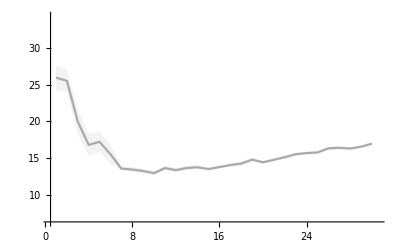

```mathematica
ErrorListPlot[
Table[Transpose[Table[
Flatten[{g,GetMeanAndSEM[100 /dayFitResults[[fittedDay]][[g]][[1]]]}]
,{g,1,30}]],{fittedDay,1,Length[dayFitResults]}],
Map[GrayLevel[1/(Length[dayFitResults]+2)+#/(Length[dayFitResults]+2)]&,Range[Length[dayFitResults]]],
{},
{True,True,False}
]
```

```mathematica
bestFiveFromEachDay=Table[Reverse[SortBy[Flatten[Table[Transpose[{dayFitResults[[day]][[generation]][[1]],dayFitResults[[day]][[generation-1]][[-1]]}],{generation,2,30}],1],First]][[1;;5]]
,{day,1,Length[dayFitResults]}]
```

{{{9.8562,{2.02697,0.68016,0.742843,0.254999,1.71026,1.00485,1.18626,0.599588}},{9.7294,{2.12527,0.639153,0.817495,0.236023,1.75992,0.926417,1.22594,0.641915}},{9.62869,{1.93311,0.712787,0.726963,0.216066,1.70947,0.996493,1.86939,0.473319}},{9.4727,{2.10364,0.744541,0.793198,0.273052,1.61731,1.38753,1.23175,0.720552}},{9.21944,{2.2124,0.572339,0.736379,0.221582,1.79995,0.886868,1.16018,0.721562}}}}

```mathematica
Mean[Map[#[[2]]&,bestFiveFromEachDay[[1]]]]
```

{2.08028,0.669796,0.763376,0.240345,1.71938,1.04043,1.3347,0.631387}

```mathematica
(*Export[NotebookDirectory[]<>"\\ga_1.mx",dayFitResults];*)
```

best fits for each day fitted

```mathematica
bestFiveFromEachDay=Table[Reverse[SortBy[Flatten[Table[Transpose[{dayFitResults[[day]][[generation]][[1]],dayFitResults[[day]][[generation-1]][[-1]]}],{generation,2,30}],1],First]][[1;;5]]
,{day,1,Length[dayFitResults]}];
```

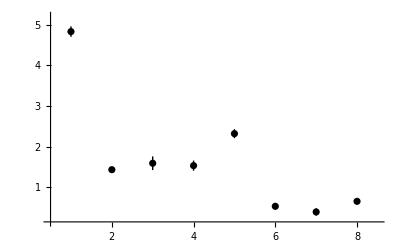

```mathematica
ErrorListPlot[
{
Join[
{Range[8]},
GetMeanAndSEM[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]]
]
},
{Black},
{},
{False,False,True}
]
```

```mathematica
bestFitMeansOverall=Mean[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]];
```

seasonal trends in correction?

```mathematica
(*{
populationFitness,
offspringFitness,
population,
offspring,
newPopulation
}*)
```

```mathematica
seasonalCorrector=Mean[Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-20;;-1]]][[2]]]
,{fittedDayN,1,Length[daysToFit]}]]];
```

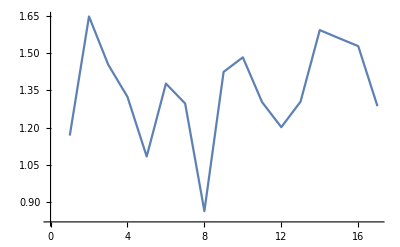

```mathematica
ListPlot[seasonalCorrector,Joined->True]
```

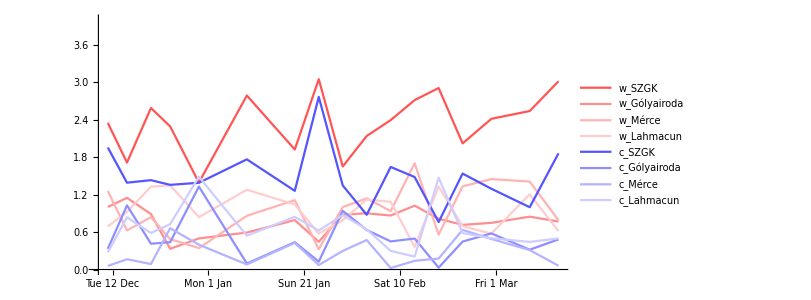

```mathematica
ListPlot[
Transpose[Table[
Transpose[{
ConstantArray[daysToFit[[fittedDayN]],8],
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
}]
,{fittedDayN,1,Length[daysToFit]}]],
Joined->True,PlotStyle->Flatten[{Map[Nest[Lighter,Red,#]&,Range[1,4]],Map[Nest[Lighter,Blue,#]&,Range[1,4]]}],
PlotLegends->Flatten[{Map["w_"<>#&,roomNames[[roomsOnCycle]]],Map["c_"<>#&,roomNames[[roomsOnCycle]]]}],
ImageSize->600,AspectRatio->0.5,Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotRange->{All,{0,4}}
]
```

```mathematica
seasonCorrectedBestFits=Map[Mean,Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
,{fittedDayN,1,Length[daysToFit]}]]]
```

```mathematica
seasonCorrectedBestFits={2.3480290895305607,0.7801014999645991,0.9513837546933651,0.9297576319359259,1.4780859968954623,0.5046262989177167,0.2679036077336363,0.6731878383370469}
```

{2.34803,0.780101,0.951384,0.929758,1.47809,0.504626,0.267904,0.673188}

##### eval fit

for one day

```mathematica
bestFitMeansOverall={3.1725563115559083,1.0683009750379302,1.29468510022947,1.278422223763722,1.9544085048287771,0.6946838470957711,0.3455993563985235,0.9222435820921898};
```

```mathematica
individual=bestFitMeansOverall
```

{4.82679,1.43645,1.59447,1.53515,2.32085,0.53767,0.398612,0.65944}

```mathematica
warmingParams=bestFitMeansOverall[[1 ;; 4]];
coolingParams=bestFitMeansOverall[[5 ;; 8]];
warmingCorrection={1,1,1,1,1,1,1,1,1,1};
coolingCorrection={1,1,1,1,1,1,1,1,1,1};
Table[
warmingCorrection[[roomsOnCycle[[roomN]]]]=warmingParams[[roomN]];
coolingCorrection[[roomsOnCycle[[roomN]]]]=coolingParams[[roomN]];
,{roomN,1,Length[roomsOnCycle]}];
warmingCorrection
coolingCorrection
```

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
```

```mathematica
roomTempStart
```

{0,0,0,0}

```mathematica
Evaluate[NumberQ[None]]
```

False

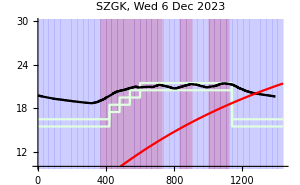
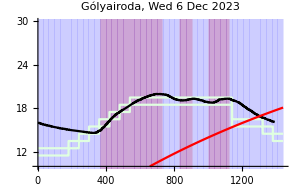
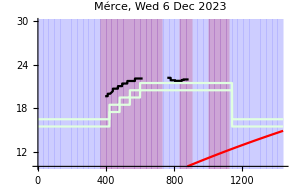
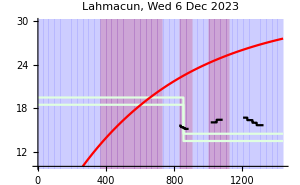

{15600.,12206.5,49042.7,30624.6}

```mathematica
simulatedDay=29;
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
{
daySimulation,
daySimulatedHeatDynamics,
dayHeatingSimulatedState,
dayRoomSimulatedTemp
}=SimulateDayForCycle[warmingCorrection,coolingCorrection];
roomSimulatedTemp=dayRoomSimulatedTemp;
heatingSimulatedState=dayHeatingSimulatedState;
simulatedHeatDynamics=daySimulatedHeatDynamics;
Table[
Quiet[Plot[
{
roomsSetTemp[[roomN]][t]-roomsLowerBuffer[[roomN]][t],
roomsSetTemp[[roomN]][t],
roomsSetTemp[[roomN]][t]+roomsUpperBuffer[[roomN]][t],
roomsTrueTemp[[roomN]][t],
roomSimulatedTemp[[roomN]][t]
},{t,0,24 60},PlotStyle->{LightGreen,None,LightGreen,Black,Red},
PlotRange->{All,{10,30}},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]],ImageSize->300,
Prolog->{
Table[If[
heatingTrueState[t]==1,
{RGBColor[1,0,0,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}],
Table[If[
heatingSimulatedState[t]==1,
{RGBColor[0,0,1,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}]
}
]
],{roomN,1,Length[roomsOnCycle]}]//Row
Join[
{100heatStockDaily[[cycle]][[dayN]][[-1]][[2]]},
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]
```

for season

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
seasonFitEvaluation=Quiet[
Module[
{roomEndTemps,heatingStateEnd},
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=None;
Table[
Check[
TimeConstrained[
Module[
{evaluationResults},
SetSimulatedDayForComparison[day,roomEndTemps,heatingStateEnd];
evaluationResults=EvaluateParameterVector[
warmingCorrection[[roomsOnCycle]],
coolingCorrection[[roomsOnCycle]]
];
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=Map[#[24 60]&,evaluationResults[[6]]];
evaluationResults[[{7,8}]]
],
5,
DateString[NormalizeDate[seasonDays[[day]]]]<>": timeout error"
],
DateString[NormalizeDate[seasonDays[[day]]]]<>": other error"]
,{day,simulatedDays}]
]
];
```

```mathematica
simulatedDays={29,30,31,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,53,54,57,59,60,61,62,63,64,65,66,67,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,98,99,103,104,105,106,107,108,111,112,114,120,121,122,125,126,127,128,129,132,133,134,135,136,139};
```

```mathematica
simulatedDays=Complement[Range[Length[seasonDays]],Flatten[Map[Position[seasonFitEvaluation,#]&,Select[seasonFitEvaluation,StringQ]]]];
```

```mathematica
seasonFitEvaluation//Length
```

80

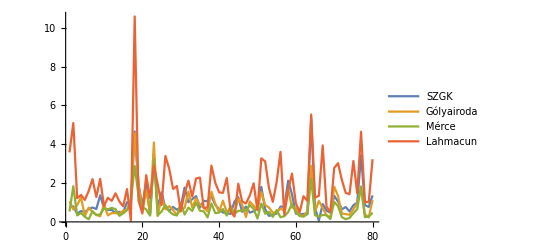

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[1]][[roomN]]
},{roomN,1,Length[roomsOnCycle]}]
,{day,1,Length[seasonFitEvaluation]}]],Joined->True,PlotRange->{All,All},PlotLegends->roomNames[[roomsOnCycle]]
]
```

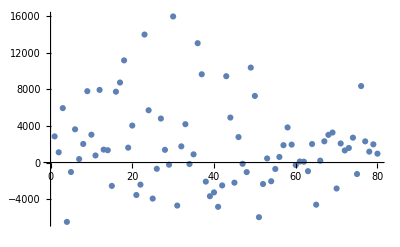

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[2]][[heatMeasureType]]
},{heatMeasureType,1,1}],{day,1,Length[seasonFitEvaluation]}]]
]
```

#### fit for multiple days cycle 1

```mathematica
daysToFit={32,37,42,57,67,72,77,82,92,122,127};
```

##### calc fit

calc

```mathematica
SetSimulatedCycle[1];
SetSimulationParameters[];
```

```mathematica
tournamentSize=10;
tournamentWinnerNumber=3;
tournamentRounds=4;
mutationMagnitude=0.1;
```

```mathematica
initialPopulationSize=30;
chromosomeLength=2Length[roomsOnCycle];
```

```mathematica
daysToFitCandidates={32,37,42,47,52,57,62,67,72,77,82,87,92,103,107,112,117,122,127};
testIndividual=RandomReal[{0,2},chromosomeLength];
dataExistenceCheck=Map[
Quiet[
{
#,
Check[
TimeConstrained[
{
SetSimulatedDayForComparison[#,ConstantArray[None,Length[roomsOnCycle]],None];
EvaluateParameterVector[
testIndividual[[1;;chromosomeLength/2]],
testIndividual[[chromosomeLength/2+1;;chromosomeLength]]
];
},
5,
"error"
],
"error"]
}
]&,
daysToFitCandidates];
errorDays=daysToFitCandidates[[Transpose[Position[dataExistenceCheck,"error"]][[1]]]];
daysToFit=Complement[daysToFitCandidates,errorDays];
```

```mathematica
dayFitResults={};
numOfGenerations=30;
tempErrorWeight=1;
heatErrorWeight=0;heatMeasureType=2;
Table[
dayN=daysToFit[[dayNN]];
startPopulation=Table[RandomReal[{0,2},chromosomeLength],{n,1,initialPopulationSize}];
Module[
{evolution},
Echo[DateString[Date[]]<>": starting "<>DateString[NormalizeDate[seasonDays[[dayN]]]]];
SetSimulatedDayForComparison[dayN,ConstantArray[None,Length[roomsOnCycle]],None];
evolution=Module[
{generations,population,newGeneration,newPopulation},
generations={};
Table[
If[
Mod[g,2]==0,
Echo[DateString[Date[]]<>": starting generation "<>ToString[g]];
];
If[g==1,population=startPopulation,population=generations[[-1]][[-1]]];
newGeneration=GenerateNewPopulation[
FitnessFunction,tempErrorWeight,heatErrorWeight,heatMeasureType,
population,
tournamentSize,tournamentWinnerNumber,tournamentRounds,
mutationMagnitude
];
If[g==1,generations={newGeneration},generations=Join[generations,{newGeneration}]];
,{g,1,numOfGenerations}];
generations
];
If[dayFitResults=={},dayFitResults={evolution},dayFitResults=Join[dayFitResults,{evolution}]];
Export[NotebookDirectory[]<>"\\ga_3.mx",dayFitResults];
]
,{dayNN,1,Length[daysToFit]}];
```

```mathematica
dayFitResults=Import[NotebookDirectory[]<>"\\ga_3.mx"];
```

```mathematica
dayFitResults//Dimensions
```

{17,30,5}

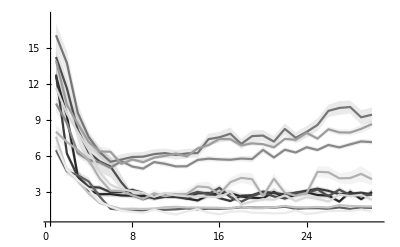

```mathematica
ErrorListPlot[
Table[Transpose[Table[
Flatten[{g,GetMeanAndSEM[100 /dayFitResults[[fittedDay]][[g]][[1]]]}]
,{g,1,30}]],{fittedDay,1,Length[dayFitResults]}],
Map[GrayLevel[1/(Length[dayFitResults]+2)+#/(Length[dayFitResults]+2)]&,Range[Length[dayFitResults]]],
{},
{True,True,False}
]
```

```mathematica
(*Export[NotebookDirectory[]<>"\\ga_1.mx",dayFitResults];*)
```

best fits for each day fitted

```mathematica
bestFiveFromEachDay=Table[Reverse[SortBy[Flatten[Table[Transpose[{dayFitResults[[day]][[generation]][[1]],dayFitResults[[day]][[generation-1]][[-1]]}],{generation,2,30}],1],First]][[1;;5]]
,{day,1,Length[dayFitResults]}];
```

```mathematica
ErrorListPlot[
{
Join[
{Range[8]},
GetMeanAndSEM[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]]
]
},
{Black},
{},
{False,False,True}
]
```

-Graphics-

```mathematica
bestFitMeansOverall=Mean[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]];
```

seasonal trends in correction?

```mathematica
(*{
populationFitness,
offspringFitness,
population,
offspring,
newPopulation
}*)
```

```mathematica
seasonalCorrector=Mean[Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-20;;-1]]][[2]]]
,{fittedDayN,1,Length[daysToFit]}]]];
```

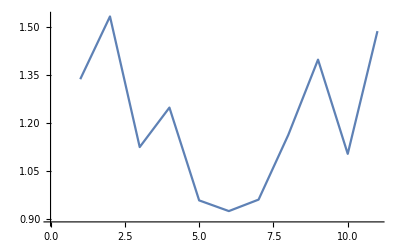

```mathematica
ListPlot[seasonalCorrector,Joined->True]
```

```mathematica
startDayN=1;
endDayN=170;
```

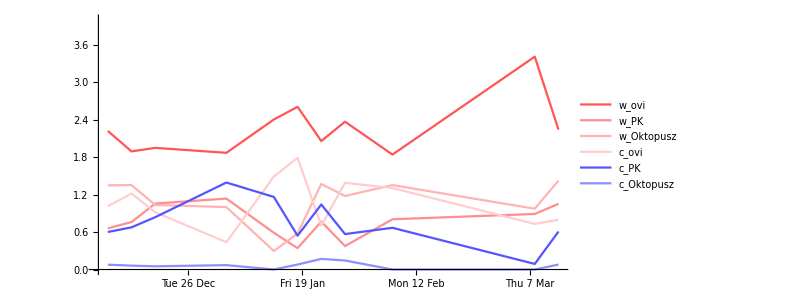

```mathematica
ListPlot[
Transpose[Table[
Transpose[{
ConstantArray[daysToFit[[fittedDayN]],Length[roomsOnCycle]2],
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
}]
,{fittedDayN,1,Length[daysToFit]}]],
Joined->True,PlotStyle->Flatten[{Map[Nest[Lighter,Red,#]&,Range[1,4]],Map[Nest[Lighter,Blue,#]&,Range[1,4]]}],
PlotLegends->Flatten[{Map["w_"<>#&,roomNames[[roomsOnCycle]]],Map["c_"<>#&,roomNames[[roomsOnCycle]]]}],
ImageSize->600,AspectRatio->0.5,Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotRange->{All,{0,4}}
]
```

```mathematica
seasonCorrectedBestFits=Map[Mean,Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
,{fittedDayN,1,Length[daysToFit]}]]]
```

```mathematica
seasonCorrectedBestFits={2.2612754125177195,0.7672629015155057,1.083197120703778,1.0727627094334409,0.7447439197371224,0.06677408038862163}
```

{2.26128,0.767263,1.0832,1.07276,0.744744,0.0667741}

##### eval fit

for one day

```mathematica
bestFitMeansOverall={3.1725563115559083,1.0683009750379302,1.29468510022947,1.278422223763722,1.9544085048287771,0.6946838470957711,0.3455993563985235,0.9222435820921898};
```

```mathematica
individual=bestFitMeansOverall
```

{4.82679,1.43645,1.59447,1.53515,2.32085,0.53767,0.398612,0.65944}

```mathematica
warmingParams=bestFitMeansOverall[[1 ;; 4]];
coolingParams=bestFitMeansOverall[[5 ;; 8]];
warmingCorrection={1,1,1,1,1,1,1,1,1,1};
coolingCorrection={1,1,1,1,1,1,1,1,1,1};
Table[
warmingCorrection[[roomsOnCycle[[roomN]]]]=warmingParams[[roomN]];
coolingCorrection[[roomsOnCycle[[roomN]]]]=coolingParams[[roomN]];
,{roomN,1,Length[roomsOnCycle]}];
warmingCorrection
coolingCorrection
```

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
```

```mathematica
roomTempStart
```

{0,0,0,0}

```mathematica
Evaluate[NumberQ[None]]
```

False

```mathematica
simulatedDay=29;
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
{
daySimulation,
daySimulatedHeatDynamics,
dayHeatingSimulatedState,
dayRoomSimulatedTemp
}=SimulateDayForCycle[warmingCorrection,coolingCorrection];
roomSimulatedTemp=dayRoomSimulatedTemp;
heatingSimulatedState=dayHeatingSimulatedState;
simulatedHeatDynamics=daySimulatedHeatDynamics;
Table[
Quiet[Plot[
{
roomsSetTemp[[roomN]][t]-roomsLowerBuffer[[roomN]][t],
roomsSetTemp[[roomN]][t],
roomsSetTemp[[roomN]][t]+roomsUpperBuffer[[roomN]][t],
roomsTrueTemp[[roomN]][t],
roomSimulatedTemp[[roomN]][t]
},{t,0,24 60},PlotStyle->{LightGreen,None,LightGreen,Black,Red},
PlotRange->{All,{10,30}},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]],ImageSize->300,
Prolog->{
Table[If[
heatingTrueState[t]==1,
{RGBColor[1,0,0,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}],
Table[If[
heatingSimulatedState[t]==1,
{RGBColor[0,0,1,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}]
}
]
],{roomN,1,Length[roomsOnCycle]}]//Row
Join[
{100heatStockDaily[[cycle]][[dayN]][[-1]][[2]]},
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]
```

-Graphics--Graphics--Graphics--Graphics-

{15600.,12206.5,49042.7,30624.6}

for season

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
seasonFitEvaluation=Quiet[
Module[
{roomEndTemps,heatingStateEnd},
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=None;
Table[
Check[
TimeConstrained[
Module[
{evaluationResults},
SetSimulatedDayForComparison[day,roomEndTemps,heatingStateEnd];
evaluationResults=EvaluateParameterVector[
warmingCorrection[[roomsOnCycle]],
coolingCorrection[[roomsOnCycle]]
];
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=Map[#[24 60]&,evaluationResults[[6]]];
evaluationResults[[{7,8}]]
],
5,
DateString[NormalizeDate[seasonDays[[day]]]]<>": timeout error"
],
DateString[NormalizeDate[seasonDays[[day]]]]<>": other error"]
,{day,simulatedDays}]
]
];
```

```mathematica
simulatedDays={29,30,31,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,53,54,57,59,60,61,62,63,64,65,66,67,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,98,99,103,104,105,106,107,108,111,112,114,120,121,122,125,126,127,128,129,132,133,134,135,136,139};
```

```mathematica
simulatedDays=Complement[Range[Length[seasonDays]],Flatten[Map[Position[seasonFitEvaluation,#]&,Select[seasonFitEvaluation,StringQ]]]];
```

```mathematica
seasonFitEvaluation//Length
```

80

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[1]][[roomN]]
},{roomN,1,Length[roomsOnCycle]}]
,{day,1,Length[seasonFitEvaluation]}]],Joined->True,PlotRange->{All,All},PlotLegends->roomNames[[roomsOnCycle]]
]
```

-Graphics-

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[2]][[heatMeasureType]]
},{heatMeasureType,1,1}],{day,1,Length[seasonFitEvaluation]}]]
]
```

-Graphics-

#### summary

```mathematica
daysFitted={
{32,37,42,57,67,72,77,82,92,122,127},
{34,38,43,47,53,63,73,78,83,88,93,98,103,108,114,122,128}
};
```

```mathematica
seasonCorrectedBestFits={
{2.2612754125177195,0.7672629015155057,1.083197120703778,1.0727627094334409,0.7447439197371224,0.06677408038862163},
{2.3480290895305607,0.7801014999645991,0.9513837546933651,0.9297576319359259,1.4780859968954623,0.5046262989177167,0.2679036077336363,0.6731878383370469}
};
```

## deploy

```mathematica
(*final jav*)
	       			       (*ovi  PK   SZGK  GI    M   k  v  t  Okt  Lah*)
       warmingCorrection={0.66,0.50,0.68,0.58,0.84,1,1,1,0.88,0.47};
       coolingCorrection={0.85,0.80,0.85,0.85,0.85,1,1,1,0.88,0.66};
roomsRadiatorOffTemp={21,      23,    25.5,22.5,22.5,26,0,24.5,20,21};
```

```mathematica
startDayN=Position[seasonDays,heatDataDays[[1]]][[1]][[1]];
endDayN=Position[seasonDays,heatDataDays[[-1]]][[1]][[1]];
simulatedDayNToDayN=Range[startDayN,endDayN];
```

```mathematica
(*{room,day}, 1-es kör: dec 24 -  jan 2 + jan 13, 2-es kör: dec 24 - jan 2*)
offdays=Flatten[{
Flatten[Table[Transpose[{ConstantArray[room,Length[Range[47,56]]],Range[47,56]}],{room,Flatten[Position[roomToCycle,1]]}],1],
Flatten[Table[Transpose[{ConstantArray[room,Length[Range[47,56]]],Range[47,56]}],{room,Flatten[Position[roomToCycle,2]]}],1],
Table[Transpose[{room,67}],{room,Flatten[Position[roomToCycle,1]]}]
},1];
```

```mathematica
simulatedRooms=Sort[Flatten[{roomsByCycle[[1]],roomsByCycle[[2]]}]];
```

```mathematica
trueHeatConsumptionForSeason=Transpose[Table[
Transpose[SortBy[Flatten[Table[
Transpose[{
roomsByCycle[[cycle]],
Total[Transpose[heatStockDaily[[cycle]][[simulatedDayNToDayN[[simulatedDayN]]]]][[2]]]roomHeatTakeupRatios[[roomsByCycle[[cycle]]]]
}],{cycle,1,2}],1],First]][[2]]
,{simulatedDayN,1,Length[simulatedDayNToDayN]}]];
```

```mathematica
trueTempDivergencesForSeason=Table[Table[
Module[
{heating,temp,setTemp,lowerBuffer,upperBuffer},
If[
Length[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&Length[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0,
heating=Transpose[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]][[1+roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]]][[2]];
temp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[1]]][[2]];setTemp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[2]]][[2]];
lowerBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[3]]][[2]];
upperBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[4]]][[2]];
{
-Map[Last,Select[Transpose[{heating,(setTemp-lowerBuffer)-temp}],#[[1]]==0&&0<#[[2]]&]],(*underheated*)
Map[Last,Select[Transpose[{heating,temp-(setTemp+upperBuffer)}],#[[1]]==1&&0<#[[2]]&]]    (*overheated*)
},
{None,None}
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}],{simulatedRoomN,1,Length[simulatedRooms]}];
```

```mathematica
trueTempUnderSamplingRatio=Table[Table[
Module[
{heating,temp,setTemp,lowerBuffer,upperBuffer},
If[
Length[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&Length[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0,
heating=Transpose[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]][[1+roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]]][[2]];
temp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[1]]][[2]];setTemp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[2]]][[2]];
lowerBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[3]]][[2]];
upperBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[4]]][[2]];
Length[Select[Transpose[{
heating,
temp,
setTemp,
lowerBuffer,
upperBuffer
}],NumberQ[Total[#]]&]]/288
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}],{simulatedRoomN,1,Length[simulatedRooms]}];
```

### replikálás

#### set temps

```mathematica
roomNames
```

{ovi,PK,SZGK,Gólyairoda,Mérce,vendégtér,kisterem,trafóház,Oktopusz,Lahmacun,Kazán közös terek,műhely}

```mathematica
noneTemps={14,14,14,14,14,14,14,14,12,14};
roomsSeasonSetTemps=Table[
Table[
If[
Length[roomTempsDaily[[room]][[dayN]]]==0||DeleteDuplicates[Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]]][[1]]=="n",
Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[noneTemps[[room]],288]}],InterpolationOrder->0],
Interpolation[Select[Transpose[{Range[0,24 60-5,5],Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]]}],NumberQ[Total[#]]&],InterpolationOrder->0]
]
,{dayN,startDayN,endDayN}],{room,1,10}];
roomsSeasonLowerBuffers=Table[
Table[
Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0.5,288]}],InterpolationOrder->0]
,{dayN,startDayN,endDayN}],{room,1,10}];
roomsSeasonUpperBuffers=Table[
Table[
Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0.5,288]}],InterpolationOrder->0]
,{dayN,startDayN,endDayN}],{room,1,10}];
```

```mathematica
startDay=69+6;
roomsOffdaySetTemps=Table[
ConstantArray[Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[{12,12,12,12,12,12,12,12,10,12}[[room]],288]}],InterpolationOrder->0],7]
,{room,1,10}];
roomsOffdayLowerBuffer=Table[
ConstantArray[Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[roomTempsDaily[[room]][[startDay]][[3]][[1]][[2]],288]}],InterpolationOrder->0],7],{room,1,10}];
roomsOffdayUpperBuffer=Table[
ConstantArray[Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[roomTempsDaily[[room]][[startDay]][[4]][[1]][[2]],288]}],InterpolationOrder->0],7],{room,1,10}];
```

#### simulation

```mathematica
cycle=2;
SetSimulatedCycle[cycle];
SetSimulationParameters[];
```

```mathematica
simulationStarted=False;
dayN=startDayN;
simulatedSeasonForCycle=Table[
If[
simulationStarted==False,
{
roomsTempStartIn={21,18,18,18};
heatingStateStartIn=0;
simulationStarted=True;
}
];
dayN=simulatedDayNToDayN[[simulatedDayN]];
dayOfWeek=DateValue[seasonDays[[dayN]],"DayNameShort"]/.dayNameToDayOfWeek;
roomsSetTempIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdaySetTemps[[room]][[dayOfWeek]],
roomsSeasonSetTemps[[room]][[simulatedDayN]]
]
],{roomN,1,Length[roomsOnCycle]}];
roomsLowerBufferIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdayLowerBuffer[[room]][[dayOfWeek]],
roomsSeasonLowerBuffers[[room]][[simulatedDayN]]
]
],{roomN,1,Length[roomsOnCycle]}];
roomsUpperBufferIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdayUpperBuffer[[room]][[dayOfWeek]],
roomsSeasonUpperBuffers[[room]][[simulatedDayN]]
]
],{roomN,1,Length[roomsOnCycle]}];
SetSimulatedDay[dayN,roomsSetTempIn,roomsLowerBufferIn,roomsUpperBufferIn,roomsTempStartIn,heatingStateStartIn];
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomsSimulatedTemp}=SimulateDayForCycle[warmingCorrection,coolingCorrection];
roomsTempStartIn=Map[#[24 60]&,roomsSimulatedTemp];
heatingStateStartIn=heatingSimulatedState[24 60];
{{dayN,seasonDays[[dayN]]},simulatedHeatDynamics,heatingSimulatedState,roomsSimulatedTemp,roomsSetTemp,roomsLowerBuffer,roomsUpperBuffer}
,{simulatedDayN,1,Length[simulatedDayNToDayN]}];
```

#### plot

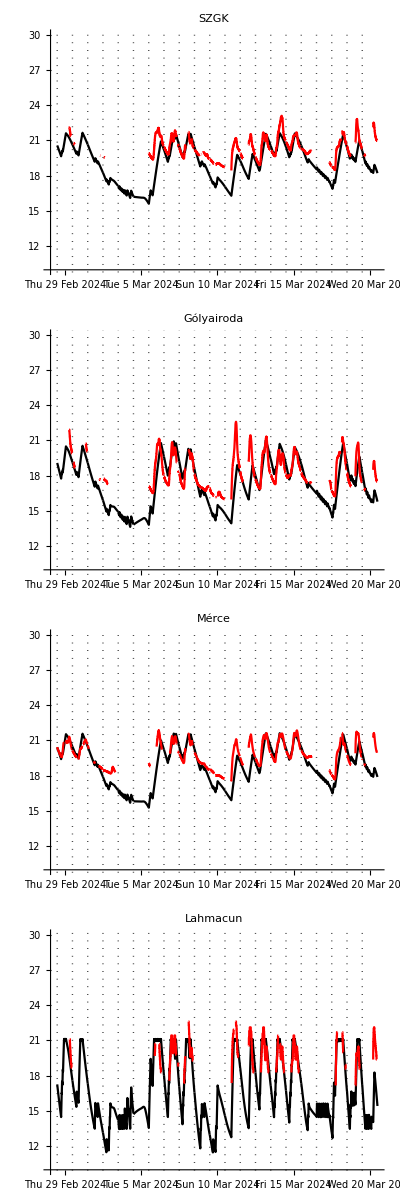

```mathematica
plotDay=100;
Table[
ListPlot[
Flatten[Table[Map[
Transpose[{
(simulatedDay-1) 24 60+Range[0,24 60-5,5],
#
}]
&,Join[
Transpose[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t]
}
,{t,0,24 60-5,5}]],
{
If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
ConstantArray[0,288]
]
}
]
],{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycle]]}],1],
PlotStyle->{Black,Red},ImageSize->1000,Joined->True,AspectRatio->0.1,PlotLabel->roomNames[[roomsOnCycle[[roomN]]]],
Ticks->{
Table[
{
(simulatedDay-1) 24 60+12 60,
Rotate[DateString[NormalizeDate[seasonDays[[startDayN+simulatedDay-1]]]],Pi/2]
}
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycle]],1}],
Automatic
},
Prolog->{
Black,Thin,Dotted,
Table[
Line[{{(simulatedDay-1) 24 60,-50},{(simulatedDay-1) 24 60,50}}]
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycle]]}]
},PlotRange->{All,{10,30}}
],{roomN,1,Length[roomsOnCycle]}]//Column
```

```mathematica
plotDay=80;
Table[
Table[
ListPlot[
Join[
Transpose[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]-simulatedSeasonForCycle[[simulatedDay]][[6]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]+simulatedSeasonForCycle[[simulatedDay]][[7]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t]
}
,{t,0,24 60,5}]],
{
If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Nothing
]
}
],
PlotStyle->{LightGreen,LightGreen,Black,Red},ImageSize->200,Joined->True,PlotLabel->DateString[NormalizeDate[seasonDays[[simulatedDay]]]]
],{roomN,1,Length[roomsOnCycle]}],{simulatedDay,plotDay,plotDay+2}]//Grid
```

#### evaluation

##### heat (cost)

```mathematica
(*simulatedHeatDynamics: loss, gain*)
```

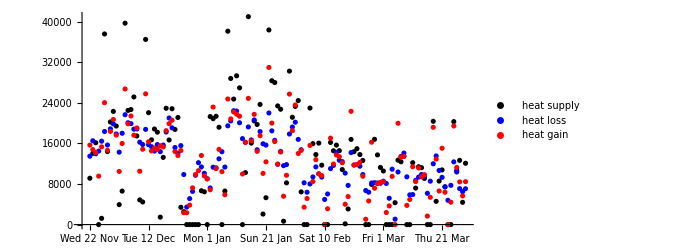
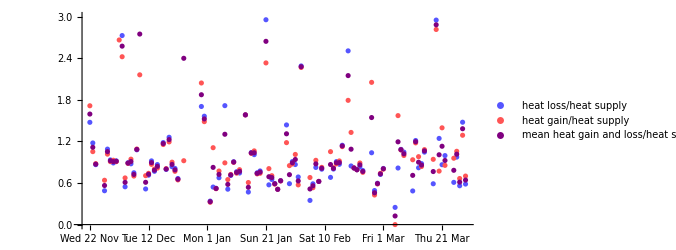

```mathematica
simulatedVsTrueHeatStockDailyForCycle=Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Total[Transpose[heatStockDaily[[cycle]][[simulatedDayNToDayN[[simulatedDay]]]]][[2]]]roomHeatTakeupRatios[[roomsOnCycle]],
Table[
Table[
Total[simulatedSeasonForCycle[[simulatedDay]][[2]][[roomN]][[heatLossOrGain]]]
,{roomN,1,Length[roomsOnCycle]}]
,{heatLossOrGain,1,2}]
}
,{simulatedDay,1,Length[simulatedSeasonForCycle]}];
{
ListPlot[
Transpose[Map[
{
{#[[1]],Total[#[[2]]]},
{#[[1]],Total[#[[3]][[1]]]},
{#[[1]],Total[#[[3]][[2]]]}
}&,simulatedVsTrueHeatStockDailyForCycle]],
PlotStyle->{Black,Blue,Red},
PlotRange->{All,All},
Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,5]
],
Automatic
},PlotLegends->Placed[{"heat supply","heat loss","heat gain"},Bottom],ImageSize->500,AspectRatio->0.5
],
ListPlot[
Quiet[Transpose[Map[
{
{#[[1]],Total[#[[3]][[1]]]/Total[#[[2]]]},
{#[[1]],Total[#[[3]][[2]]]/Total[#[[2]]]},
{#[[1]],Mean[{Total[#[[3]][[1]]]/Total[#[[2]]],Total[#[[3]][[2]]]/Total[#[[2]]]}]}
}&,simulatedVsTrueHeatStockDailyForCycle]]],
PlotStyle->{Lighter[Blue],Lighter[Red],Purple},
PlotRange->{All,{0,3}},
Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,5]
],
Automatic
},PlotLegends->Placed[{"heat loss/heat supply","heat gain/heat supply","mean heat gain and loss/heat supply"},Bottom],ImageSize->500,AspectRatio->0.5
]
}//Row
```

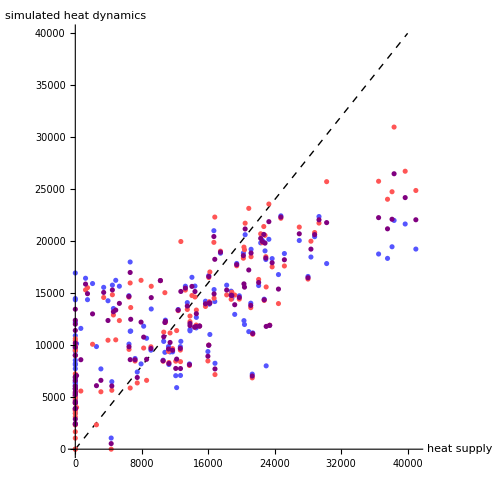

```mathematica
ListPlot[
{
Transpose[{
Map[Total,Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]],Map[Total[#[[3]][[1]]]&,simulatedVsTrueHeatStockDailyForCycle]
}],
Transpose[{
Map[Total,Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]],Map[Total[#[[3]][[2]]]&,simulatedVsTrueHeatStockDailyForCycle]
}],
Transpose[{
Map[Total,Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]],Map[Mean[{Total[#[[3]][[1]]],Total[#[[3]][[2]]]}]&,simulatedVsTrueHeatStockDailyForCycle]
}]
},AspectRatio->1,PlotRange->{0,40000},AxesLabel->{"heat supply","simulated heat dynamics"},PlotStyle->{Lighter[Blue],Lighter[Red],Purple},ImageSize->500,Prolog->{Black,Thin,Dashed,Line[{{0,0},{40000,40000}}]}
]
```

```mathematica
Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]]]/100
```

16759.3

```mathematica
Total[Map[Total[#[[3]][[1]]]&,simulatedVsTrueHeatStockDailyForCycle]]/100
100(Total[Map[Total[#[[3]][[1]]]&,simulatedVsTrueHeatStockDailyForCycle]]/100)/(Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]]]/100)-100
```

16558.9

-1.19592

```mathematica
Total[Map[Total[#[[3]][[2]]]&,simulatedVsTrueHeatStockDailyForCycle]]/100
100(Total[Map[Total[#[[3]][[2]]]&,simulatedVsTrueHeatStockDailyForCycle]]/100)/(Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]]]/100)-100
```

16552.

-1.23654

```mathematica
Total[Map[Mean[{Total[#[[3]][[1]]],Total[#[[3]][[2]]]}]&,simulatedVsTrueHeatStockDailyForCycle]]/100
100(Total[Map[Mean[{Total[#[[3]][[1]]],Total[#[[3]][[2]]]}]&,simulatedVsTrueHeatStockDailyForCycle]]/100)/(Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]]]/100)-100
```

16555.4

-1.21623

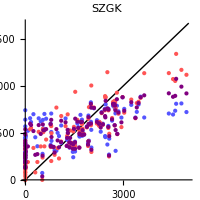
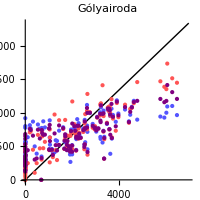
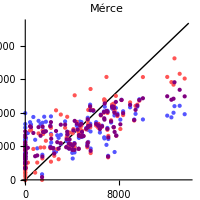
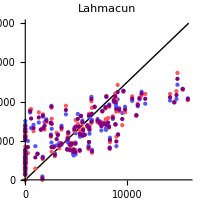

```mathematica
Table[
Module[
{heatData,maxHeat},
heatData=Table[Map[
{
#[[2]][[roomN]],
{#[[3]][[1]][[roomN]],#[[3]][[2]][[roomN]],Mean[{#[[3]][[1]][[roomN]],#[[3]][[2]][[roomN]]}]}[[type]]
}
&,simulatedVsTrueHeatStockDailyForCycle],{type,1,3}];
maxHeat=Ceiling[Max[heatData],1000];
ListPlot[
heatData,
AspectRatio->1,PlotRange->{{0,maxHeat},{0,maxHeat}},Prolog->{Thin,Black,Line[{{0,0},{maxHeat,maxHeat}}]},
PlotStyle->{{PointSize->0.025,Lighter[Blue]},{PointSize->0.025,Lighter[Red]},{PointSize->0.025,Purple}},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]],ImageSize->200
]
]
,{roomN,1,Length[roomsOnCycle]}]//Row
```

##### temperature (performance)

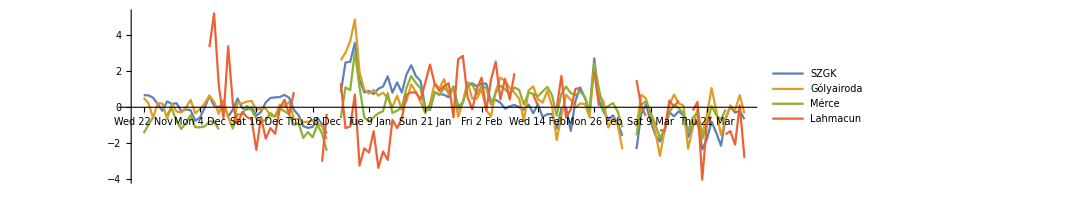

```mathematica
simulatedDailyTempVsTrueTempForCycle=Quiet[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Table[If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Map[
#[[2]]-#[[1]]&,
Select[
Transpose[{
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Table[simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t],{t,0,24 60-5,5}]
}],
NumberQ[Total[Flatten[#]]]
&]
],
{}
]
,{roomN,1,Length[roomsOnCycle]}]
},{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
ListPlot[
Transpose[Table[Map[
{
simulatedDailyTempVsTrueTempForCycle[[simulatedDay]][[1]],
Mean[#]
}
&,simulatedDailyTempVsTrueTempForCycle[[simulatedDay]][[2]]
],{simulatedDay,1,Length[simulatedSeasonForCycle]}]],Joined->True,AspectRatio->0.25,ImageSize->800,PlotRange->{All,All},
Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotLegends->roomNames[[roomsOnCycle]]
]
```

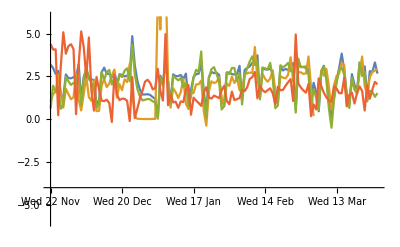
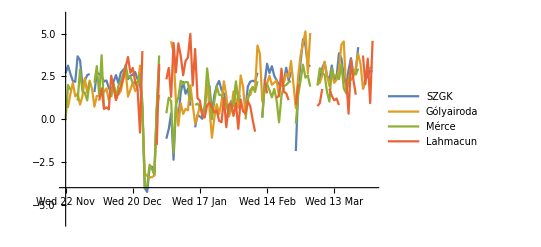

```mathematica
simulatedDailyTempDivergenceVsTrueDivergenceForCycle=Quiet[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Table[Map[
If[
#[[1]]<#[[2]],
#[[1]]-#[[2]],
#[[1]]-#[[3]]
]&,
Select[
Table[{
simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]-simulatedSeasonForCycle[[simulatedDay]][[6]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]+simulatedSeasonForCycle[[simulatedDay]][[7]][[roomN]][t]
},{t,0,24 60-5,5}],
Between[
#[[1]],
#[[2;;3]]
]==False&]
],{roomN,1,Length[roomsOnCycle]}],
Table[If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Map[
If[
#[[1]]<#[[2]],
#[[1]]-#[[2]],
#[[1]]-#[[3]]
]&,
Select[
Transpose[{
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[2]]][[2]]-Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[3]]][[2]],
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[2]]][[2]]+Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[4]]][[2]]
}],
Between[
#[[1]],
#[[2;;3]]
]==False&]
],
{}
]
,{roomN,1,Length[roomsOnCycle]}]
},{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
Table[
ListPlot[
Transpose[Table[
Map[{
simulatedDailyTempDivergenceVsTrueDivergenceForCycle[[simulatedDay]][[1]],
Mean[#]
}&,simulatedDailyTempDivergenceVsTrueDivergenceForCycle[[simulatedDay]][[simulatedOrTrue]]]
,{simulatedDay,1,Length[simulatedSeasonForCycle]}]],
Joined->True,ImageSize->400,Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotRange->{All,{-6,6}},AxesOrigin->{startDayN,-4},PlotLegends->{None,roomNames[[roomsOnCycle]]}[[simulatedOrTrue-1]]
],{simulatedOrTrue,2,3}]//Row
```

##### heat vs temp (cost vs performance)

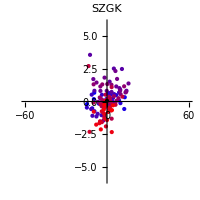
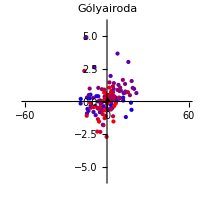
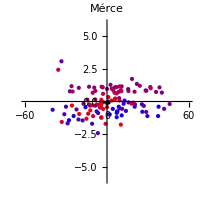
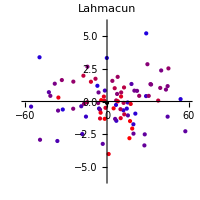

```mathematica
simulatedVsTrueHeatStockDailyForCycle=Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Total[Transpose[heatStockDaily[[cycle]][[simulatedDayNToDayN[[simulatedDay]]]]][[2]]]roomHeatTakeupRatios[[roomsOnCycle]],
Table[
Table[
Total[simulatedSeasonForCycle[[simulatedDay]][[2]][[roomN]][[heatLossOrGain]]]
,{roomN,1,Length[roomsOnCycle]}]
,{heatLossOrGain,1,2}]
}
,{simulatedDay,1,Length[simulatedSeasonForCycle]}];
simulatedDailyTempVsTrueTempForCycle=Quiet[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Table[If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Map[
#[[2]]-#[[1]]&,
Select[
Transpose[{
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Table[simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t],{t,0,24 60-5,5}]
}],
NumberQ[Total[Flatten[#]]]
&]
],
{}
]
,{roomN,1,Length[roomsOnCycle]}]
},{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
heatSumError=Transpose[Table[
(simulatedVsTrueHeatStockDailyForCycle[[simulatedDay]][[2]]-simulatedVsTrueHeatStockDailyForCycle[[simulatedDay]][[3]][[2]])/100
,{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
dailyTempError=Transpose[Table[
Map[If[Length[#]!=0,Mean[#],Missing]&,simulatedDailyTempVsTrueTempForCycle[[simulatedDay]][[2]]]
,{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
Table[
Module[
{errorMeans,errorSEMs},
errorMeans={
Mean[RemoveOutliers[DeleteCases[heatSumError[[roomN]],Missing],3]],
Mean[RemoveOutliers[DeleteCases[dailyTempError[[roomN]],Missing],3]]
};
errorSEMs={
StandardError[RemoveOutliers[DeleteCases[heatSumError[[roomN]],Missing],3]],
StandardError[RemoveOutliers[DeleteCases[dailyTempError[[roomN]],Missing],3]]
};
ListPlot[
{},
PlotRange->{{-60,60},{-6,6}},
Epilog->{
{
Table[
Module[
{data},
data=Transpose[{heatSumError[[roomN]],dailyTempError[[roomN]]}];
{
RGBColor[n/Length[data],0,1-n/Length[data]],
PointSize->0.0125,
data[[n]]//If[NumberQ[Total[#]],Point[#],Nothing]&
}
],{n,1,Length[Transpose[{heatSumError[[roomN]],dailyTempError[[roomN]]}]]}],
Black,PointSize->0.025,
Point[{errorMeans[[1]],errorMeans[[2]]}],
RGBColor[0,0,0,0],
EdgeForm[{Thick,Black}],
Ellipsoid[{errorMeans[[1]],errorMeans[[2]]},15{errorSEMs[[1]],errorSEMs[[2]]}]
}
},AspectRatio->1,ImageSize->200,PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]
]
],{roomN,1,Length[roomsOnCycle]}]//Row
```

### időprogram

#### set room schedules

```mathematica
offdaySchedule=Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0,288]}],InterpolationOrder->0];
ondayScheduleForOktopusz=Interpolation[{{0,0},{15 60-1,0},{15 60,1},{24 60-1,1},{24 60,0}},InterpolationOrder->0];
ondayMondaySchedule=Interpolation[{{0,0},{1,0},{2,1},{17 60-1,1},{17 60,0}},InterpolationOrder->0];
ondaySchedule=Interpolation[{{0,0},{6 60-1,0},{6 60,1},{16 60-1,1},{16 60,0}},InterpolationOrder->0];
```

```mathematica
roomsWorkDays={
{1,1,1,1,0,0,0},(*ovi*)
{1,1,1,1,1,0,0},(*PK*)
{1,1,1,1,1,0,0},(*SZGK*)
{1,1,1,1,1,0,0},(*Gólyairoda*)
{1,1,1,1,1,0,0},(*Mérce*)
{1,1,1,1,1,0,0},(*vendégtér*)
{1,1,1,1,1,0,0},(*kisterem*)
{1,1,1,1,1,0,0},(*trafóház*)
{1,1,1,1,1,0,0},(*Oktopusz*)
{1,1,1,1,1,0,0}(*Lahmacun*)
};
```

```mathematica
roomsWeeklySchedules=Table[Table[
If[
roomsWorkDays[[room]][[dayOfWeek]]==1,
If[room==9,
ondayScheduleForOktopusz,
If[dayOfWeek==1,ondayMondaySchedule,ondaySchedule]
],
offdaySchedule
]
,{dayOfWeek,1,7}],{room,1,10}];
```

```mathematica
roomsOffdaySchedules=Table[offdaySchedule,{room,1,10}];
```

#### simulation

```mathematica
simulatedSeasonForCycles=
Table[
SetSimulatedCycle[cycle];
SetSimulationParameters[];
simulatedDayNToDayN=Range[startDayN,endDayN];
simulationStarted=False;
dayN=startDayN;
Table[
If[
simulationStarted==False,
{
roomsTempStartIn={{20,20,20},{21,18,18,18}}[[cycle]];
heatingStateStartIn=0;
simulationStarted=True;
}
];
dayN=simulatedDayNToDayN[[simulatedDayN]];
dayOfWeek=DateValue[seasonDays[[dayN]],"DayNameShort"]/.dayNameToDayOfWeek;
roomsSchedulesIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdaySchedules[[room]],
roomsWeeklySchedules[[room]][[dayOfWeek]]
]
],{roomN,1,Length[roomsOnCycle]}];
SetSimulatedDayWithTimedHeating[dayN,roomsSchedulesIn,roomsTempStartIn];
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomsSimulatedTemp}=SimulateDayForCycleWithTimedHeating[warmingCorrection,coolingCorrection];
roomsTempStartIn=Map[#[24 60]&,roomsSimulatedTemp];
heatingStateStartIn=heatingSimulatedState[24 60];
{
{dayN,seasonDays[[dayN]]},
simulatedHeatDynamics,
heatingSimulatedState,roomsSimulatedTemp
}
,{simulatedDayN,1,Length[simulatedDayNToDayN]}]
,{cycle,1,2}];
```

#### plot

```mathematica
cycle=1;
```

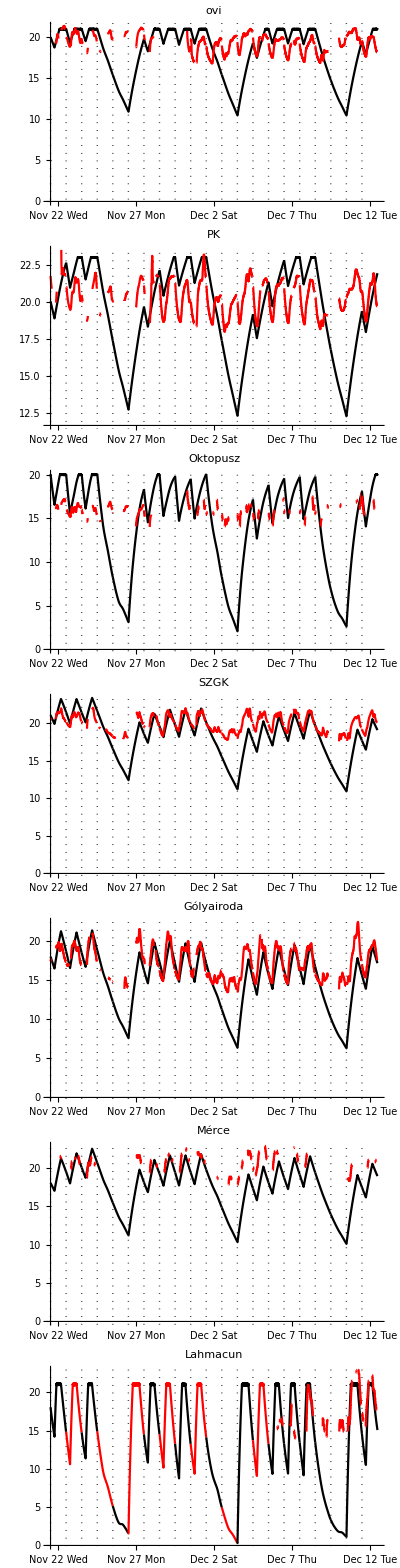

```mathematica
plotDay=1;
Table[Table[
ListPlot[
Flatten[Table[Map[
Transpose[{
(simulatedDay-1) 24 60+Range[0,24 60-5,5],
#
}]
&,Join[
Transpose[Table[
{
simulatedSeasonForCycles[[cycle]][[simulatedDay]][[4]][[roomN]][t]
}
,{t,0,24 60-5,5}]],
{
If[
Length[roomTempsDaily[[roomsByCycle[[cycle]][[roomN]]]][[simulatedSeasonForCycles[[cycle]][[simulatedDay]][[1]][[1]]]]]!=0,
Transpose[roomTempsDaily[[roomsByCycle[[cycle]][[roomN]]]][[simulatedSeasonForCycles[[cycle]][[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Nothing
]
}
]
],{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycles[[cycle]]]]}],1],
PlotStyle->{Black,Red},ImageSize->1000,Joined->True,AspectRatio->0.1,PlotLabel->roomNames[[roomsByCycle[[cycle]][[roomN]]]],
Ticks->{
Table[
{
(simulatedDay-1) 24 60+12 60,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[startDayN+simulatedDay-1]]]]," "][[{3,2,1}]]," "],Pi/2]
}
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycles[[cycle]]]],1}],
Automatic
},
Prolog->{
Black,Thin,Dotted,
Table[
Line[{{(simulatedDay-1) 24 60,-50},{(simulatedDay-1) 24 60,50}}]
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycles[[cycle]]]]}]
}
],{roomN,1,Length[roomsByCycle[[cycle]]]}],{cycle,1,2}]//Flatten//Column
```

#### comparison with past season

##### heat

```mathematica
simulatedHeatConsumptionForSeason=Transpose[Table[
Transpose[SortBy[Flatten[Table[
Transpose[{
roomsByCycle[[cycle]],
Table[Total[simulatedSeasonForCycles[[cycle]][[simulatedDayN]][[2]][[roomN]][[2]]],{roomN,1,Length[roomsByCycle[[cycle]]]}]
}],{cycle,1,2}],1],First]][[2]]
,{simulatedDayN,1,Length[simulatedSeasonForCycles[[1]]]}]];
```

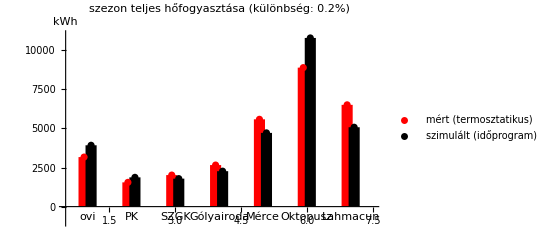

```mathematica
ListPlot[{
Transpose[{Range[7]-0.08,Map[Total,trueHeatConsumptionForSeason]/100}],
Transpose[{Range[7]+0.08,Map[Total,simulatedHeatConsumptionForSeason]/100}]
},PlotStyle->{Red,Black},PlotRange->{{0.5,7.5},{-1000,11000}},
Filling->Axis,FillingStyle->{Thickness[0.02]},Ticks->{None,Automatic},
PlotLabel->"szezon teljes hőfogyasztása (különbség: "<>ToString[Round[100 Total[Map[Total,simulatedHeatConsumptionForSeason]]/Total[Map[Total,trueHeatConsumptionForSeason]]-100,0.1]]<>"%)",AxesLabel->{None,"kWh"},PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
ImageSize->400,Epilog->{Black,Map[Text[roomNames[[simulatedRooms]][[#]],{#,-650}]&,Range[7]]}
]
```

misc

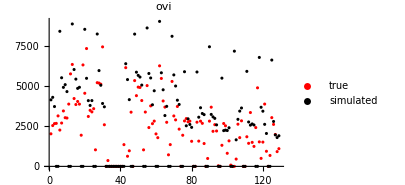
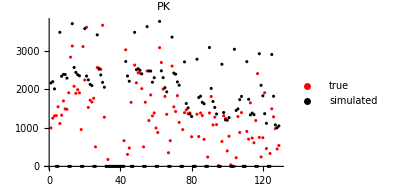
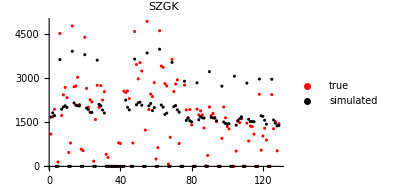
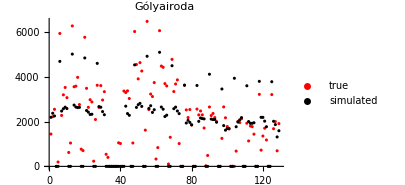
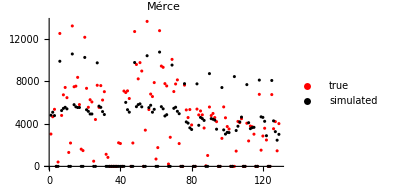
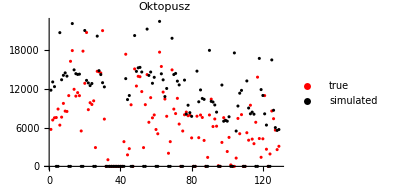
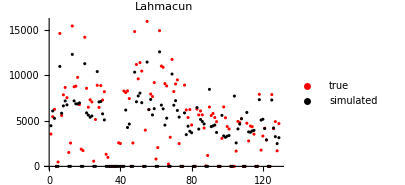

```mathematica
Table[
ListPlot[
{
trueHeatConsumptionForSeason[[simulatedRoomN]],
simulatedHeatConsumptionForSeason[[simulatedRoomN]]
},PlotStyle->{Red,Black},PlotLegends->Placed[{"true","simulated"},Bottom],ImageSize->300,PlotLabel->roomNames[[simulatedRooms[[simulatedRoomN]]]]
],{simulatedRoomN,1,Length[simulatedRooms]}]//Row
```

##### temp

céltartás

```mathematica
simulatedTempDivergencesForSeason=Table[Table[
Module[
{heating,temp,setTemp,lowerBuffer,upperBuffer},
If[
Length[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&Length[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0,
heating=Map[simulatedSeasonForCycles[[roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]][[simulatedDayN]][[3]][#]&,Range[5,24 60,5]];
temp=Map[simulatedSeasonForCycles[[roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]][[simulatedDayN]][[4]][[Position[roomsByCycle[[roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]],simulatedRooms[[simulatedRoomN]]][[1]][[1]]]][#]&,Range[5,24 60,5]];setTemp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[2]]][[2]];
lowerBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[3]]][[2]];
upperBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[4]]][[2]];
{
-Map[Last,Select[Transpose[{heating,(setTemp-lowerBuffer)-temp}],#[[1]]==0&&0<#[[2]]&]],(*underheated*)
Map[Last,Select[Transpose[{heating,temp-(setTemp+upperBuffer)}],#[[1]]==1&&0<#[[2]]&]]    (*overheated*)
},
{None,None,None}
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}],{simulatedRoomN,1,Length[simulatedRooms]}];
```

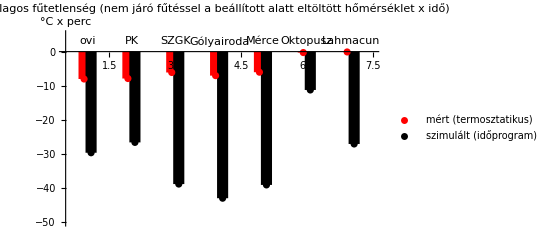
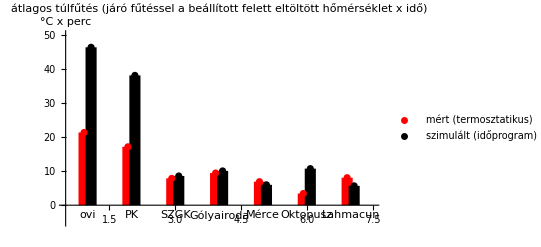

```mathematica
Quiet[Table[ListPlot[
{
Table[
{
simulatedRoomN-0.08,
Mean[Select[Table[
Total[trueTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]]/5
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
}
,{simulatedRoomN,1,Length[simulatedRooms]}],
Table[
{
simulatedRoomN+0.08,
Mean[Select[Table[
Total[
simulatedTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//RandomSample[#,Round[Length[#]trueTempUnderSamplingRatio[[simulatedRoomN]][[simulatedDayN]]]]&
]/5
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
}
,{simulatedRoomN,1,Length[simulatedRooms]}]
},PlotStyle->{Red,Black},PlotRange->{{0.5,7.5},{{-50,5},{-5,50}}[[underOrOverHeated]]},
Filling->Axis,FillingStyle->{Thickness[0.02]},Ticks->{None,Automatic},
PlotLabel->{"átlagos fűtetlenség\n(nem járó fűtéssel a beállított alatt eltöltött hőmérséklet x idő)","átlagos túlfűtés\n(járó fűtéssel a beállított felett eltöltött hőmérséklet x idő)"}[[underOrOverHeated]],AxesLabel->{None,"°C x perc"},PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
ImageSize->400,Epilog->{Black,Map[Text[roomNames[[simulatedRooms]][[#]],{#,{3,-3}[[underOrOverHeated]]}]&,Range[7]]}
],{underOrOverHeated,1,2}]]//Row
```

hőmérsékletek

##### heat vs temp

```mathematica
plotData={
Transpose[{
Map[Total,trueHeatConsumptionForSeason]/100,
Total[Abs[Table[Table[
Mean[Select[Table[
Total[trueTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]]/5
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
,{simulatedRoomN,1,Length[simulatedRooms]}],{underOrOverHeated,1,2}]]]
}],
Transpose[{
Map[Total,simulatedHeatConsumptionForSeason]/100,
Total[Abs[Table[Table[
Quiet[Mean[Select[Table[
Total[
simulatedTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//RandomSample[#,Round[Length[#]trueTempUnderSamplingRatio[[simulatedRoomN]][[simulatedDayN]]]]&
]/5
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]]
,{simulatedRoomN,1,Length[simulatedRooms]}],{underOrOverHeated,1,2}]]]
}]
}
```

{{{3166.11,29.318},{1549.87,24.9897},{2015.8,13.9776},{2655.96,16.4579},{5581.62,12.9203},{8883.96,3.6922},{6505.9,8.14828}},{{3921.03,75.9638},{1870.49,64.5908},{1788.05,47.3346},{2265.15,53.024},{4713.64,45.1448},{10782.6,22.2075},{5073.81,32.3159}}}

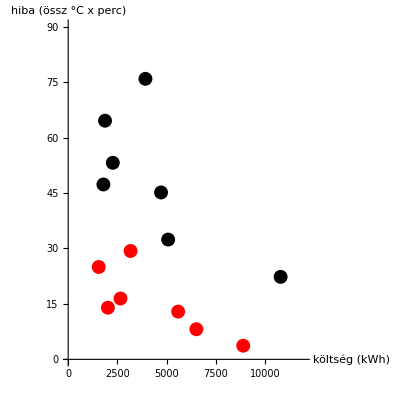

```mathematica
Module[
{plotData},
plotData={
Transpose[{
Map[Total,trueHeatConsumptionForSeason]/100,
Total[Abs[Table[Table[
Mean[Select[Table[
Total[trueTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]]/5
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
,{simulatedRoomN,1,Length[simulatedRooms]}],{underOrOverHeated,1,2}]]]
}],
Transpose[{
Map[Total,simulatedHeatConsumptionForSeason]/100,
Total[Abs[Table[Table[
Quiet[Mean[Select[Table[
Total[
simulatedTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//RandomSample[#,Round[Length[#]trueTempUnderSamplingRatio[[simulatedRoomN]][[simulatedDayN]]]]&
]/5
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]]
,{simulatedRoomN,1,Length[simulatedRooms]}],{underOrOverHeated,1,2}]]]
}]
};
ListPlot[
plotData,
AspectRatio->1,PlotRange->{{0,12000},{0,90}},PlotStyle->{{PointSize->0.025,Red},{PointSize->0.025,Black}},
AxesLabel->{"költség\n(kWh)","hiba\n(össz °C x perc)"},ImageSize->400,
Prolog->{
Line[
]
}
]
]
```

### fejlesztés: Lahmacun lyuk betömve

### fejlesztés: Oktopusz lyuk betömve

### fejlesztés: Gólyairoda leszigetelve

### fejlesztés: termosztatikus radiátorok

### fejlesztés: Lahmacun, Oktopusz, Gólyairoda

### fejlesztés: Lahmacun, Oktopusz, Gólyairoda, termosztatikus radiátorok

### spórolás: csökkentett komfort

## forintosítás számlák alapján, viszonyítás korábbi évekhez

## milyen hőigény érhető el, ha le is van szigetelve az épület? hogy viszonyul ez egy hőszivattyúhoz?